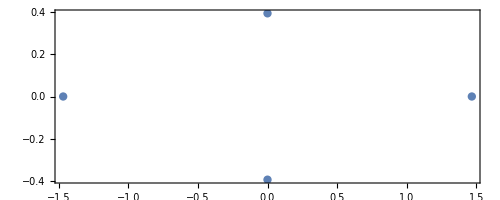

```mathematica
rootPlot[poly_,x_,opts___]/;PolynomialQ[poly,x]:=ListPlot[Map[Composition[Through,{Re,Im}],x/.NSolve[poly,x]],opts,AspectRatio->Automatic]
rootPlot[3x^4-6x^2-1,x,Axes->None,Frame->True,PlotStyle->AbsolutePointSize[6]]
```

```mathematica
Animate[rootPlot[3x^4-4*(-1+ⅇ^(2π*ⅈ*t))*x^3-6x^2+12*(-1+ⅇ^(2π*ⅈ*t))x-4*(-1+ⅇ^(2π*ⅈ*t))^2-1,x,Axes->None,Frame->True,PlotStyle->AbsolutePointSize[6], PlotRange-> {{-4, 4}, {-4, 4}}], {t, 0, 1}]
```

```mathematica
Animate[rootPlot[3x^4-4*(1-ⅇ^(2π*ⅈ*t))*x^3-6x^2+12*(1-ⅇ^(2π*ⅈ*t))x-4*(1-ⅇ^(2π*ⅈ*t))^2-1,x,Axes->None,Frame->True,PlotStyle->AbsolutePointSize[6], PlotRange-> {{-4, 4}, {-4, 4}}], {t, 0, 1}]
```

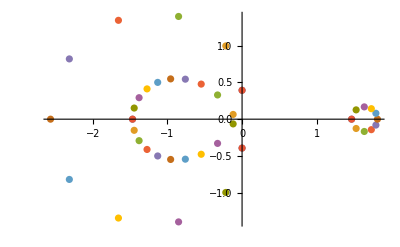

```mathematica
ListPlot[Table[Map[Composition[Through,{Re,Im}],x/.NSolve[3x^4-4*(-1+ⅇ^(2π*ⅈ*t/10))*x^3-6x^2+12*(-1+ⅇ^(2π*ⅈ*t/10))x-4*(-1+ⅇ^(2π*ⅈ*t/10))^2-1,x]], {t,0, 10}]]
```

```mathematica
f[x_, t_]:= {3x^4-4*(-1+ⅇ^(2π*ⅈ*t))*x^3-6x^2+12*(-1+ⅇ^(2π*ⅈ*t))x-4*(-1+ⅇ^(2π*ⅈ*t))^2-1, t}
g[x_, t_]:={3x^4-4*(1-ⅇ^(2π*ⅈ*t))*x^3-6x^2+12*(1-ⅇ^(2π*ⅈ*t))x-4*(1-ⅇ^(2π*ⅈ*t))^2-1, t}
```

```mathematica
ListPointPlot3D[Table[{Re[x/.NSolve[f[x, t][[1]], x][[i]]],Im[x/.NSolve[f[x, t][[1]], x][[i]]] , f[x, t][[2]]}, {i, 4}, {t, 0, 1, .01}] , ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[{Re[x/.NSolve[g[x, t][[1]], x][[i]]],Im[x/.NSolve[g[x, t][[1]], x][[i]]] , g[x, t][[2]]}, {i, 4}, {t, 0, 1, .01}] , ColorFunction->"Rainbow"]
```

```mathematica
T=Table[{x/.NSolve[f[x, t][[1]]==0, x][[i]], t}, {i, 1, 4}, {t, 0,1, .01}]
NSolve[x-T[[1]][[30]][[1]]==0, x]
X=Table[{Re[x/.NSolve[x^2-(T[[i]][[j]][[1]]^2-1)*(T[[i]][[j]][[1]]-(-1+ⅇ^(2*π*ⅈ*j/100)))==0, x][[k]]], Im[x/.NSolve[x^2-(T[[i]][[j]][[1]]^2-1)*(T[[i]][[j]][[1]]-(-1+ⅇ^(2*π*ⅈ*j/100)))==0, x][[k]]], (j-1)/100}, {k, 1, 2}, {i, 1, 4}, {j, 1, 100}]
Y=Join[X[[1]][[1]], X[[1]][[2]], X[[1]][[3]], X[[1]][[4]], X[[2]][[1]], X[[2]][[2]], X[[2]][[3]], X[[2]][[4]]]
ListPointPlot3D[Y, ColorFunction-> "Rainbow"]
```

{{{-1.46789,0.},{-1.46767-0.0153303 ⅈ,0.01},{-1.467-0.0306498 ⅈ,0.02},{-1.46588-0.045948 ⅈ,0.03},{-1.46433-0.061214 ⅈ,0.04},{-1.46232-0.0764373 ⅈ,0.05},{-1.45988-0.0916071 ⅈ,0.06},{-1.45699-0.106713 ⅈ,0.07},{-1.45366-0.121744 ⅈ,0.08},{-1.44989-0.136689 ⅈ,0.09},{-1.44568-0.151538 ⅈ,0.1},{-1.44104-0.166281 ⅈ,0.11},{-1.43596-0.180907 ⅈ,0.12},{-1.43044-0.195404 ⅈ,0.13},{-1.4245-0.209764 ⅈ,0.14},{-1.41813-0.223974 ⅈ,0.15},{-1.41134-0.238025 ⅈ,0.16},{-1.40412-0.251907 ⅈ,0.17},{-1.39649-0.265608 ⅈ,0.18},{-1.38844-0.279119 ⅈ,0.19},{-1.37997-0.292428 ⅈ,0.2},{-1.3711-0.305527 ⅈ,0.21},{-1.36182-0.318404 ⅈ,0.22},{-1.35214-0.331049 ⅈ,0.23},{-1.34206-0.343452 ⅈ,0.24},{-1.33159-0.355603 ⅈ,0.25},{-1.33425+1.42723 ⅈ,0.26},{-1.41603+1.4144 ⅈ,0.27},{-1.49726+1.39648 ⅈ,0.28},{-1.5776+1.37353 ⅈ,0.29},{-1.65673+1.3456 ⅈ,0.3},{-1.73432+1.31277 ⅈ,0.31},{-1.81006+1.27516 ⅈ,0.32},{-1.88364+1.23287 ⅈ,0.33},{-1.95476+1.18605 ⅈ,0.34},{-2.02314+1.13487 ⅈ,0.35},{-2.0885+1.0795 ⅈ,0.36},{-2.15057+1.02013 ⅈ,0.37},{-2.2091+0.956994 ⅈ,0.38},{-2.26386+0.890303 ⅈ,0.39},{-2.31463+0.820304 ⅈ,0.4},{-2.3612+0.747254 ⅈ,0.41},{-2.40339+0.67142 ⅈ,0.42},{-2.44102+0.593084 ⅈ,0.43},{-2.47395+0.512535 ⅈ,0.44},{-2.50203+0.430073 ⅈ,0.45},{-2.52517+0.346003 ⅈ,0.46},{-2.54326+0.260641 ⅈ,0.47},{-2.55624+0.174304 ⅈ,0.48},{-2.56404+0.0873154 ⅈ,0.49},{-2.56665,0.5},{-2.56404-0.0873154 ⅈ,0.51},{-2.55624-0.174304 ⅈ,0.52},{-2.54326-0.260641 ⅈ,0.53},{-2.52517-0.346003 ⅈ,0.54},{-2.50203-0.430073 ⅈ,0.55},{-2.47395-0.512535 ⅈ,0.56},{-2.44102-0.593084 ⅈ,0.57},{-2.40339-0.67142 ⅈ,0.58},{-2.3612-0.747254 ⅈ,0.59},{-2.31463-0.820304 ⅈ,0.6},{-2.26386-0.890303 ⅈ,0.61},{-2.2091-0.956994 ⅈ,0.62},{-2.15057-1.02013 ⅈ,0.63},{-2.0885-1.0795 ⅈ,0.64},{-2.02314-1.13487 ⅈ,0.65},{-1.95476-1.18605 ⅈ,0.66},{-1.88364-1.23287 ⅈ,0.67},{-1.81006-1.27516 ⅈ,0.68},{-1.73432-1.31277 ⅈ,0.69},{-1.65673-1.3456 ⅈ,0.7},{-1.5776-1.37353 ⅈ,0.71},{-1.49726-1.39648 ⅈ,0.72},{-1.41603-1.4144 ⅈ,0.73},{-1.33425-1.42723 ⅈ,0.74},{-1.33159+0.355603 ⅈ,0.75},{-1.34206+0.343452 ⅈ,0.76},{-1.35214+0.331049 ⅈ,0.77},{-1.36182+0.318404 ⅈ,0.78},{-1.3711+0.305527 ⅈ,0.79},{-1.37997+0.292428 ⅈ,0.8},{-1.38844+0.279119 ⅈ,0.81},{-1.39649+0.265608 ⅈ,0.82},{-1.40412+0.251907 ⅈ,0.83},{-1.41134+0.238025 ⅈ,0.84},{-1.41813+0.223974 ⅈ,0.85},{-1.4245+0.209764 ⅈ,0.86},{-1.43044+0.195404 ⅈ,0.87},{-1.43596+0.180907 ⅈ,0.88},{-1.44104+0.166281 ⅈ,0.89},{-1.44568+0.151538 ⅈ,0.9},{-1.44989+0.136689 ⅈ,0.91},{-1.45366+0.121744 ⅈ,0.92},{-1.45699+0.106713 ⅈ,0.93},{-1.45988+0.0916071 ⅈ,0.94},{-1.46232+0.0764373 ⅈ,0.95},{-1.46433+0.061214 ⅈ,0.96},{-1.46588+0.045948 ⅈ,0.97},{-1.467+0.0306498 ⅈ,0.98},{-1.46767+0.0153303 ⅈ,0.99},{-1.46789,1.}},{{0.-0.39332 ⅈ,0.},{-0.00185681+0.451457 ⅈ,0.01},{-0.00764978+0.511213 ⅈ,0.02},{-0.0176741+0.572219 ⅈ,0.03},{-0.0321648+0.634061 ⅈ,0.04},{-0.0512905+0.696294 ⅈ,0.05},{-0.0751528+0.758458 ⅈ,0.06},{-0.10379+0.820095 ⅈ,0.07},{-0.137183+0.880753 ⅈ,0.08},{-0.175262+0.939999 ⅈ,0.09},{-0.217914+0.997418 ⅈ,0.1},{-0.26499+1.05262 ⅈ,0.11},{-0.31631+1.10525 ⅈ,0.12},{-0.371666+1.15496 ⅈ,0.13},{-0.430828+1.20145 ⅈ,0.14},{-0.493548+1.24441 ⅈ,0.15},{-0.559561+1.2836 ⅈ,0.16},{-0.628585+1.31878 ⅈ,0.17},{-0.70033+1.34972 ⅈ,0.18},{-0.77449+1.37625 ⅈ,0.19},{-0.850755+1.39819 ⅈ,0.2},{-0.928804+1.41541 ⅈ,0.21},{-1.00831+1.42778 ⅈ,0.22},{-1.08894+1.43521 ⅈ,0.23},{-1.17037+1.43762 ⅈ,0.24},{-1.25225+1.43497 ⅈ,0.25},{-1.32073-0.367491 ⅈ,0.26},{-1.30949-0.379107 ⅈ,0.27},{-1.29786-0.390441 ⅈ,0.28},{-1.28587-0.401482 ⅈ,0.29},{-1.2735-0.41222 ⅈ,0.3},{-1.26076-0.422646 ⅈ,0.31},{-1.24767-0.43275 ⅈ,0.32},{-1.23422-0.442521 ⅈ,0.33},{-1.22042-0.45195 ⅈ,0.34},{-1.20628-0.461027 ⅈ,0.35},{-1.1918-0.469742 ⅈ,0.36},{-1.17699-0.478085 ⅈ,0.37},{-1.16186-0.486046 ⅈ,0.38},{-1.1464-0.493616 ⅈ,0.39},{-1.13063-0.500785 ⅈ,0.4},{-1.11456-0.507543 ⅈ,0.41},{-1.09819-0.513881 ⅈ,0.42},{-1.08152-0.519787 ⅈ,0.43},{-1.06456-0.525253 ⅈ,0.44},{-1.04733-0.530269 ⅈ,0.45},{-1.02982-0.534824 ⅈ,0.46},{-1.01205-0.53891 ⅈ,0.47},{-0.994021-0.542514 ⅈ,0.48},{-0.975738-0.545628 ⅈ,0.49},{-0.957212-0.548241 ⅈ,0.5},{-0.975738+0.545628 ⅈ,0.51},{-0.994021+0.542514 ⅈ,0.52},{-1.01205+0.53891 ⅈ,0.53},{-1.02982+0.534824 ⅈ,0.54},{-1.04733+0.530269 ⅈ,0.55},{-1.06456+0.525253 ⅈ,0.56},{-1.08152+0.519787 ⅈ,0.57},{-1.09819+0.513881 ⅈ,0.58},{-1.11456+0.507543 ⅈ,0.59},{-1.13063+0.500785 ⅈ,0.6},{-1.1464+0.493616 ⅈ,0.61},{-1.16186+0.486046 ⅈ,0.62},{-1.17699+0.478085 ⅈ,0.63},{-1.1918+0.469742 ⅈ,0.64},{-1.20628+0.461027 ⅈ,0.65},{-1.22042+0.45195 ⅈ,0.66},{-1.23422+0.442521 ⅈ,0.67},{-1.24767+0.43275 ⅈ,0.68},{-1.26076+0.422646 ⅈ,0.69},{-1.2735+0.41222 ⅈ,0.7},{-1.28587+0.401482 ⅈ,0.71},{-1.29786+0.390441 ⅈ,0.72},{-1.30949+0.379107 ⅈ,0.73},{-1.32073+0.367491 ⅈ,0.74},{-1.25225-1.43497 ⅈ,0.75},{-1.17037-1.43762 ⅈ,0.76},{-1.08894-1.43521 ⅈ,0.77},{-1.00831-1.42778 ⅈ,0.78},{-0.928804-1.41541 ⅈ,0.79},{-0.850755-1.39819 ⅈ,0.8},{-0.77449-1.37625 ⅈ,0.81},{-0.70033-1.34972 ⅈ,0.82},{-0.628585-1.31878 ⅈ,0.83},{-0.559561-1.2836 ⅈ,0.84},{-0.493548-1.24441 ⅈ,0.85},{-0.430828-1.20145 ⅈ,0.86},{-0.371666-1.15496 ⅈ,0.87},{-0.31631-1.10525 ⅈ,0.88},{-0.26499-1.05262 ⅈ,0.89},{-0.217914-0.997418 ⅈ,0.9},{-0.175262-0.939999 ⅈ,0.91},{-0.137183-0.880753 ⅈ,0.92},{-0.10379-0.820095 ⅈ,0.93},{-0.0751528-0.758458 ⅈ,0.94},{-0.0512905-0.696294 ⅈ,0.95},{-0.0321648-0.634061 ⅈ,0.96},{-0.0176741-0.572219 ⅈ,0.97},{-0.00764978-0.511213 ⅈ,0.98},{-0.00185681-0.451457 ⅈ,0.99},{0.+0.39332 ⅈ,1.}},{{0.+0.39332 ⅈ,0.},{-0.00173575-0.337108 ⅈ,0.01},{-0.00668869-0.283059 ⅈ,0.02},{-0.0144707-0.231334 ⅈ,0.03},{-0.0246997-0.182024 ⅈ,0.04},{-0.0370146-0.135156 ⅈ,0.05},{-0.0510867-0.0907071 ⅈ,0.06},{-0.0666254-0.0486155 ⅈ,0.07},{-0.0833797-0.00879335 ⅈ,0.08},{-0.101137+0.0288627 ⅈ,0.09},{-0.119718+0.0644636 ⅈ,0.1},{-0.138977+0.0981214 ⅈ,0.11},{-0.158791+0.129946 ⅈ,0.12},{-0.179061+0.160042 ⅈ,0.13},{-0.199703+0.188508 ⅈ,0.14},{-0.22065+0.215434 ⅈ,0.15},{-0.241847+0.240905 ⅈ,0.16},{-0.263244+0.264998 ⅈ,0.17},{-0.284805+0.287781 ⅈ,0.18},{-0.306495+0.30932 ⅈ,0.19},{-0.328285+0.329671 ⅈ,0.2},{-0.350152+0.348888 ⅈ,0.21},{-0.372073+0.367019 ⅈ,0.22},{-0.39403+0.384108 ⅈ,0.23},{-0.416005+0.400195 ⅈ,0.24},{-0.437984+0.415317 ⅈ,0.25},{-0.459952+0.429507 ⅈ,0.26},{-0.481897+0.442798 ⅈ,0.27},{-0.503806+0.455217 ⅈ,0.28},{-0.525667+0.466792 ⅈ,0.29},{-0.547471+0.477547 ⅈ,0.3},{-0.569207+0.487505 ⅈ,0.31},{-0.590864+0.496689 ⅈ,0.32},{-0.612434+0.505117 ⅈ,0.33},{-0.633906+0.512809 ⅈ,0.34},{-0.655272+0.519784 ⅈ,0.35},{-0.676523+0.526058 ⅈ,0.36},{-0.69765+0.531646 ⅈ,0.37},{-0.718644+0.536566 ⅈ,0.38},{-0.739497+0.540831 ⅈ,0.39},{-0.7602+0.544455 ⅈ,0.4},{-0.780745+0.547453 ⅈ,0.41},{-0.801124+0.549836 ⅈ,0.42},{-0.821328+0.551618 ⅈ,0.43},{-0.84135+0.552811 ⅈ,0.44},{-0.861182+0.553426 ⅈ,0.45},{-0.880816+0.553476 ⅈ,0.46},{-0.900243+0.552972 ⅈ,0.47},{-0.919457+0.551924 ⅈ,0.48},{-0.938449+0.550343 ⅈ,0.49},{-0.957212+0.548241 ⅈ,0.5},{-0.938449-0.550343 ⅈ,0.51},{-0.919457-0.551924 ⅈ,0.52},{-0.900243-0.552972 ⅈ,0.53},{-0.880816-0.553476 ⅈ,0.54},{-0.861182-0.553426 ⅈ,0.55},{-0.84135-0.552811 ⅈ,0.56},{-0.821328-0.551618 ⅈ,0.57},{-0.801124-0.549836 ⅈ,0.58},{-0.780745-0.547453 ⅈ,0.59},{-0.7602-0.544455 ⅈ,0.6},{-0.739497-0.540831 ⅈ,0.61},{-0.718644-0.536566 ⅈ,0.62},{-0.69765-0.531646 ⅈ,0.63},{-0.676523-0.526058 ⅈ,0.64},{-0.655272-0.519784 ⅈ,0.65},{-0.633906-0.512809 ⅈ,0.66},{-0.612434-0.505117 ⅈ,0.67},{-0.590864-0.496689 ⅈ,0.68},{-0.569207-0.487505 ⅈ,0.69},{-0.547471-0.477547 ⅈ,0.7},{-0.525667-0.466792 ⅈ,0.71},{-0.503806-0.455217 ⅈ,0.72},{-0.481897-0.442798 ⅈ,0.73},{-0.459952-0.429507 ⅈ,0.74},{-0.437984-0.415317 ⅈ,0.75},{-0.416005-0.400195 ⅈ,0.76},{-0.39403-0.384108 ⅈ,0.77},{-0.372073-0.367019 ⅈ,0.78},{-0.350152-0.348888 ⅈ,0.79},{-0.328285-0.329671 ⅈ,0.8},{-0.306495-0.30932 ⅈ,0.81},{-0.284805-0.287781 ⅈ,0.82},{-0.263244-0.264998 ⅈ,0.83},{-0.241847-0.240905 ⅈ,0.84},{-0.22065-0.215434 ⅈ,0.85},{-0.199703-0.188508 ⅈ,0.86},{-0.179061-0.160042 ⅈ,0.87},{-0.158791-0.129946 ⅈ,0.88},{-0.138977-0.0981214 ⅈ,0.89},{-0.119718-0.0644636 ⅈ,0.9},{-0.101137-0.0288627 ⅈ,0.91},{-0.0833797+0.00879335 ⅈ,0.92},{-0.0666254+0.0486155 ⅈ,0.93},{-0.0510867+0.0907071 ⅈ,0.94},{-0.0370146+0.135156 ⅈ,0.95},{-0.0246997+0.182024 ⅈ,0.96},{-0.0144707+0.231334 ⅈ,0.97},{-0.00668869+0.283059 ⅈ,0.98},{-0.00173575+0.337108 ⅈ,0.99},{0.-0.39332 ⅈ,1.}},{{1.46789,0.},{1.46863-0.0152978 ⅈ,0.01},{1.47082-0.030393 ⅈ,0.02},{1.47441-0.0450953 ⅈ,0.03},{1.4793-0.0592365 ⅈ,0.04},{1.48537-0.0726777 ⅈ,0.05},{1.49248-0.0853114 ⅈ,0.06},{1.50051-0.0970612 ⅈ,0.07},{1.5093-0.107878 ⅈ,0.08},{1.51872-0.117737 ⅈ,0.09},{1.52867-0.12663 ⅈ,0.1},{1.53902-0.134566 ⅈ,0.11},{1.54968-0.141562 ⅈ,0.12},{1.56057-0.147643 ⅈ,0.13},{1.5716-0.15284 ⅈ,0.14},{1.58271-0.157186 ⅈ,0.15},{1.59385-0.160714 ⅈ,0.16},{1.60496-0.163461 ⅈ,0.17},{1.616-0.165462 ⅈ,0.18},{1.62692-0.166751 ⅈ,0.19},{1.6377-0.167361 ⅈ,0.2},{1.64831-0.167327 ⅈ,0.21},{1.65871-0.166679 ⅈ,0.22},{1.66889-0.165448 ⅈ,0.23},{1.67883-0.163664 ⅈ,0.24},{1.6885-0.161354 ⅈ,0.25},{1.69788-0.158547 ⅈ,0.26},{1.70697-0.155268 ⅈ,0.27},{1.71576-0.151543 ⅈ,0.28},{1.72421-0.147396 ⅈ,0.29},{1.73234-0.142851 ⅈ,0.3},{1.74012-0.137931 ⅈ,0.31},{1.74755-0.132658 ⅈ,0.32},{1.75462-0.127054 ⅈ,0.33},{1.76132-0.121139 ⅈ,0.34},{1.76765-0.114935 ⅈ,0.35},{1.77359-0.108462 ⅈ,0.36},{1.77915-0.101738 ⅈ,0.37},{1.78431-0.0947845 ⅈ,0.38},{1.78908-0.0876189 ⅈ,0.39},{1.79344-0.0802604 ⅈ,0.4},{1.7974-0.0727272 ⅈ,0.41},{1.80096-0.0650374 ⅈ,0.42},{1.8041-0.057209 ⅈ,0.43},{1.80683-0.0492597 ⅈ,0.44},{1.80914-0.0412071 ⅈ,0.45},{1.81103-0.0330685 ⅈ,0.46},{1.81251-0.0248613 ⅈ,0.47},{1.81356-0.0166027 ⅈ,0.48},{1.81419-0.00830991 ⅈ,0.49},{1.8144,0.5},{1.81419+0.00830991 ⅈ,0.51},{1.81356+0.0166027 ⅈ,0.52},{1.81251+0.0248613 ⅈ,0.53},{1.81103+0.0330685 ⅈ,0.54},{1.80914+0.0412071 ⅈ,0.55},{1.80683+0.0492597 ⅈ,0.56},{1.8041+0.057209 ⅈ,0.57},{1.80096+0.0650374 ⅈ,0.58},{1.7974+0.0727272 ⅈ,0.59},{1.79344+0.0802604 ⅈ,0.6},{1.78908+0.0876189 ⅈ,0.61},{1.78431+0.0947845 ⅈ,0.62},{1.77915+0.101738 ⅈ,0.63},{1.77359+0.108462 ⅈ,0.64},{1.76765+0.114935 ⅈ,0.65},{1.76132+0.121139 ⅈ,0.66},{1.75462+0.127054 ⅈ,0.67},{1.74755+0.132658 ⅈ,0.68},{1.74012+0.137931 ⅈ,0.69},{1.73234+0.142851 ⅈ,0.7},{1.72421+0.147396 ⅈ,0.71},{1.71576+0.151543 ⅈ,0.72},{1.70697+0.155268 ⅈ,0.73},{1.69788+0.158547 ⅈ,0.74},{1.6885+0.161354 ⅈ,0.75},{1.67883+0.163664 ⅈ,0.76},{1.66889+0.165448 ⅈ,0.77},{1.65871+0.166679 ⅈ,0.78},{1.64831+0.167327 ⅈ,0.79},{1.6377+0.167361 ⅈ,0.8},{1.62692+0.166751 ⅈ,0.81},{1.616+0.165462 ⅈ,0.82},{1.60496+0.163461 ⅈ,0.83},{1.59385+0.160714 ⅈ,0.84},{1.58271+0.157186 ⅈ,0.85},{1.5716+0.15284 ⅈ,0.86},{1.56057+0.147643 ⅈ,0.87},{1.54968+0.141562 ⅈ,0.88},{1.53902+0.134566 ⅈ,0.89},{1.52867+0.12663 ⅈ,0.9},{1.51872+0.117737 ⅈ,0.91},{1.5093+0.107878 ⅈ,0.92},{1.50051+0.0970612 ⅈ,0.93},{1.49248+0.0853114 ⅈ,0.94},{1.48537+0.0726777 ⅈ,0.95},{1.4793+0.0592365 ⅈ,0.96},{1.47441+0.0450953 ⅈ,0.97},{1.47082+0.030393 ⅈ,0.98},{1.46863+0.0152978 ⅈ,0.99},{1.46789,1.}}}

{{x→-1.5776+1.37353 ⅈ}}

{{{{-0.0278577,1.30133,0},{-0.0877998,1.29834,1/100},{-0.147513,1.29247,1/50},{-0.206854,1.28375,3/100},{-0.265681,1.27219,1/25},{-0.323851,1.25782,1/20},{-0.381226,1.24069,3/50},{-0.437668,1.22083,7/100},{-0.493043,1.1983,2/25},{-0.547219,1.17316,9/100},{-0.600068,1.14547,1/10},{-0.651464,1.11531,11/100},{-0.701287,1.08275,3/25},{-0.74942,1.04788,13/100},{-0.795752,1.01079,7/50},{-0.840174,0.971572,3/20},{-0.882586,0.930331,4/25},{-0.92289,0.887172,17/100},{-0.960997,0.842208,9/50},{-0.996821,0.795552,19/100},{-1.03028,0.747327,1/5},{-1.06131,0.697654,21/100},{-1.08985,0.646662,11/50},{-1.11582,0.594481,23/100},{-1.13918,0.541245,6/25},{-1.1599,0.487088,1/4},{-1.38844,-0.0896117,13/50},{-1.41002,-0.172266,27/100},{-1.42554,-0.258273,7/25},{-1.43465,-0.347104,29/100},{-1.43701,-0.438191,3/10},{-1.43238,-0.530939,31/100},{-1.42055,-0.624726,8/25},{-1.40136,-0.718912,33/100},{-1.37475,-0.812845,17/50},{-1.34068,-0.905864,7/20},{-1.29919,-0.997307,9/25},{-1.25038,-1.08652,37/100},{-1.19443,-1.17284,19/50},{-1.13154,-1.25565,39/100},{-1.062,-1.33434,2/5},{-0.986145,-1.40832,41/100},{-0.904367,-1.47703,21/50},{-0.817105,-1.53997,43/100},{-0.724845,-1.59667,11/25},{-0.628114,-1.64668,9/20},{-0.527479,-1.68963,23/50},{-0.423539,-1.7252,47/100},{-0.316921,-1.75312,12/25},{-0.208275,-1.77317,49/100},{-0.0982674,-1.7852,1/2},{-0.0124232,1.78911,51/100},{-0.123113,1.78488,13/25},{-0.233118,1.77254,53/100},{-0.341761,1.75218,27/50},{-0.448374,1.72396,11/20},{-0.552311,1.68809,14/25},{-0.652944,1.64485,57/100},{-0.749677,1.59456,29/50},{-0.841944,1.5376,59/100},{-0.929221,1.4744,3/5},{-1.01102,1.40544,61/100},{-1.08691,1.33123,31/50},{-1.1565,1.25233,63/100},{-1.21946,1.16931,16/25},{-1.27551,1.0828,13/20},{-1.32442,0.993413,33/50},{-1.36605,0.901807,67/100},{-1.4003,0.808637,17/25},{-1.42713,0.714562,69/100},{-1.44656,0.620243,7/10},{-1.45869,0.526329,71/100},{-1.46367,0.433459,18/25},{-1.4617,0.342248,73/100},{-1.45306,0.253291,37/50},{-1.14973,-0.543117,3/4},{-1.12594,-0.596527,19/25},{-1.09955,-0.648852,77/100},{-1.07062,-0.69996,39/50},{-1.03919,-0.749722,79/100},{-1.00533,-0.798012,4/5},{-0.96913,-0.844705,81/100},{-0.930656,-0.889684,41/50},{-0.889997,-0.932832,83/100},{-0.847245,-0.974041,21/25},{-0.802498,-1.0132,17/20},{-0.755858,-1.05022,43/50},{-0.707434,-1.085,87/100},{-0.657339,-1.11744,22/25},{-0.60569,-1.14748,89/100},{-0.552609,-1.17502,9/10},{-0.498222,-1.20001,91/100},{-0.442657,-1.22236,23/25},{-0.386047,-1.24204,93/100},{-0.328528,-1.25898,47/50},{-0.270236,-1.27315,19/20},{-0.211313,-1.2845,24/25},{-0.151898,-1.29302,97/100},{-0.0921358,-1.29867,49/50},{-0.032169,-1.30144,99/100}},{{-0.512053,-0.514273,0},{-0.439288,0.446861,1/100},{-0.446367,0.457606,1/50},{-0.457223,0.469837,3/100},{-0.472195,0.482925,1/25},{-0.491509,0.496189,1/20},{-0.515267,0.508919,3/50},{-0.543458,0.520407,7/100},{-0.575957,0.529962,2/25},{-0.612548,0.536929,9/100},{-0.652923,0.540698,1/10},{-0.696706,0.540713,11/100},{-0.743456,0.536479,3/25},{-0.792679,0.527562,13/100},{-0.843839,0.513596,7/50},{-0.896365,0.494279,3/20},{-0.94966,0.46938,4/25},{-1.00311,0.438734,17/100},{-1.05608,0.402247,9/50},{-1.10794,0.359892,19/100},{-1.15806,0.311706,1/5},{-1.20581,0.257796,21/100},{-1.25058,0.198331,11/50},{-1.29178,0.13354,23/100},{-1.32884,0.0637134,6/25},{-1.36123,-0.0108031,1/4},{-1.17792,0.432148,13/50},{-1.19322,0.376565,27/100},{-1.20577,0.32048,7/25},{-1.21557,0.264032,29/100},{-1.2226,0.207365,3/10},{-1.22686,0.150621,31/100},{-1.22837,0.0939401,8/25},{-1.22713,0.0374639,33/100},{-1.22316,-0.0186678,17/50},{-1.21651,-0.074317,7/20},{-1.20719,-0.129347,9/25},{-1.19527,-0.183625,37/100},{-1.18078,-0.237018,19/50},{-1.16379,-0.289399,39/100},{-1.14436,-0.340643,2/5},{-1.12257,-0.390628,41/100},{-1.09848,-0.439238,21/50},{-1.07219,-0.486361,43/100},{-1.04379,-0.531888,11/25},{-1.01336,-0.575717,9/20},{-0.981011,-0.617752,23/50},{-0.94685,-0.6579,47/100},{-0.910987,-0.696076,12/25},{-0.873535,-0.732202,49/100},{-0.834615,-0.766204,1/2},{-0.929112,0.707198,51/100},{-0.964891,0.668165,13/25},{-0.998936,0.627183,53/100},{-1.03114,0.584339,27/50},{-1.06139,0.539725,11/20},{-1.0896,0.493438,14/25},{-1.11567,0.445582,57/100},{-1.13951,0.396266,29/50},{-1.16104,0.345602,59/100},{-1.18017,0.293707,3/5},{-1.19685,0.240704,61/100},{-1.21101,0.186717,31/50},{-1.22259,0.131876,63/100},{-1.23155,0.0763121,16/25},{-1.23783,0.0201592,13/20},{-1.24141,-0.0364459,33/50},{-1.24226,-0.0933649,67/100},{-1.24035,-0.150458,17/25},{-1.23567,-0.207584,69/100},{-1.22823,-0.264602,7/10},{-1.21801,-0.32137,71/100},{-1.20503,-0.377746,18/25},{-1.1893,-0.433589,73/100},{-1.17086,-0.488759,37/50},{-1.43806,0.167148,3/4},{-1.41707,0.0843454,19/25},{-1.39053,0.00536913,77/100},{-1.35889,-0.0693413,39/50},{-1.32267,-0.139396,79/100},{-1.2824,-0.204458,4/5},{-1.23866,-0.264248,81/100},{-1.19204,-0.318549,41/50},{-1.14317,-0.367206,83/100},{-1.09268,-0.410129,21/25},{-1.04119,-0.4473,17/20},{-0.989366,-0.478767,43/50},{-0.937821,-0.504652,87/100},{-0.887179,-0.52515,22/25},{-0.838034,-0.540528,89/100},{-0.79095,-0.551126,9/10},{-0.74645,-0.557359,91/100},{-0.705002,-0.559711,23/25},{-0.667012,-0.558733,93/100},{-0.632804,-0.555037,47/50},{-0.602614,-0.549287,19/20},{-0.576566,-0.542182,24/25},{-0.554668,-0.53444,97/100},{-0.5368,-0.526771,49/50},{-0.522717,-0.519847,99/100}},{{-0.43554,0.438148,0},{-0.504347,-0.510561,1/100},{-0.499064,-0.509107,1/50},{-0.495632,-0.510183,3/100},{-0.493473,-0.513938,1/25},{-0.49203,-0.520412,1/20},{-0.490791,-0.52955,3/50},{-0.489296,-0.541225,7/100},{-0.487147,-0.555256,2/25},{-0.484006,-0.571425,9/100},{-0.479593,-0.589495,1/10},{-0.473679,-0.609213,11/100},{-0.466083,-0.630326,3/25},{-0.456661,-0.65258,13/100},{-0.445308,-0.675726,7/50},{-0.431944,-0.699524,3/20},{-0.41652,-0.723742,4/25},{-0.399005,-0.748156,17/100},{-0.37939,-0.772552,9/50},{-0.357683,-0.796727,19/100},{-0.333906,-0.820486,1/5},{-0.308095,-0.843646,21/100},{-0.280299,-0.86603,11/50},{-0.250576,-0.887473,23/100},{-0.218995,-0.907817,6/25},{-0.185633,-0.926916,1/4},{-0.150576,-0.94463,13/50},{-0.113916,-0.960828,27/100},{-0.075754,-0.97539,7/25},{-0.0361948,-0.988202,29/100},{-0.00465,0.99916,3/10},{-0.0466642,1.00817,31/100},{-0.0897271,1.01514,8/25},{-0.133714,1.02,33/100},{-0.178496,1.02267,17/50},{-0.223942,1.0231,7/20},{-0.269918,1.02123,9/25},{-0.316288,1.01702,37/100},{-0.362914,1.01042,19/50},{-0.409657,1.00143,39/100},{-0.456376,0.990007,2/5},{-0.502931,0.976151,41/100},{-0.549182,0.959859,21/50},{-0.594989,0.941136,43/100},{-0.640213,0.919997,11/25},{-0.684715,0.896464,9/20},{-0.728359,0.870567,23/50},{-0.771012,0.842343,47/100},{-0.812541,0.811838,12/25},{-0.852817,0.779105,49/100},{-0.891715,0.744202,1/2},{-0.794349,-0.798016,51/100},{-0.752866,-0.827581,13/25},{-0.710293,-0.854845,53/100},{-0.666765,-0.879764,27/50},{-0.622416,-0.902302,11/20},{-0.577384,-0.92243,14/25},{-0.531807,-0.940125,57/100},{-0.485824,-0.955375,29/50},{-0.439577,-0.968174,59/100},{-0.393208,-0.978524,3/5},{-0.346856,-0.986437,61/100},{-0.300663,-0.991932,31/50},{-0.254769,-0.995036,63/100},{-0.209312,-0.995785,16/25},{-0.164429,-0.994224,13/20},{-0.120256,-0.990404,33/50},{-0.076924,-0.984387,67/100},{-0.0345627,-0.976242,17/25},{-0.00670179,0.966047,69/100},{-0.0467476,0.953887,7/10},{-0.0854569,0.939858,71/100},{-0.122717,0.924062,18/25},{-0.158419,0.90661,73/100},{-0.192463,0.887621,37/50},{-0.224751,0.867223,3/4},{-0.255196,0.845551,19/25},{-0.283715,0.822752,77/100},{-0.310235,0.798976,39/50},{-0.334692,0.774387,79/100},{-0.357029,0.749154,4/5},{-0.377203,0.723456,81/100},{-0.395181,0.697481,41/50},{-0.410941,0.671427,83/100},{-0.424478,0.645501,21/25},{-0.435802,0.619918,17/20},{-0.444942,0.594905,43/50},{-0.451948,0.570698,87/100},{-0.456892,0.54754,22/25},{-0.459878,0.525685,89/100},{-0.46104,0.505392,9/10},{-0.460549,0.486923,91/100},{-0.458623,0.470542,23/25},{-0.455526,0.456503,93/100},{-0.451582,0.445046,47/50},{-0.447172,0.436382,19/20},{-0.44274,0.430677,24/25},{-0.438791,0.428034,97/100},{-0.435881,0.428473,49/50},{-0.434597,0.431911,99/100}},{{-1.30308,0.0278203,0},{-1.30734,0.0875839,1/100},{-1.31618,0.146722,1/50},{-1.32947,0.204787,3/100},{-1.34702,0.261373,1/25},{-1.36861,0.316118,1/20},{-1.39396,0.368717,3/50},{-1.42278,0.418913,7/100},{-1.45479,0.466502,2/25},{-1.4897,0.511318,9/100},{-1.52723,0.553234,1/10},{-1.5671,0.59215,11/100},{-1.60906,0.627991,3/25},{-1.65285,0.660703,13/100},{-1.69826,0.690246,7/50},{-1.74504,0.716594,3/20},{-1.79297,0.739732,4/25},{-1.84187,0.759656,17/100},{-1.89151,0.776369,9/50},{-1.94172,0.789883,19/100},{-1.99229,0.800215,1/5},{-2.04305,0.807393,21/100},{-2.09382,0.811447,11/50},{-2.14444,0.812419,23/100},{-2.19472,0.810352,6/25},{-2.24451,0.805299,1/4},{-2.29365,0.797319,13/50},{-2.34198,0.786474,27/100},{-2.38936,0.772836,7/25},{-2.43564,0.756481,29/100},{-2.48068,0.737491,3/10},{-2.52435,0.715955,31/100},{-2.56651,0.691965,8/25},{-2.60704,0.665622,33/100},{-2.64583,0.637029,17/50},{-2.68275,0.606297,7/20},{-2.71771,0.573538,9/25},{-2.7506,0.538874,37/100},{-2.78132,0.502426,19/50},{-2.80979,0.464323,39/100},{-2.83593,0.424696,2/5},{-2.85966,0.38368,41/100},{-2.88091,0.341413,21/50},{-2.89963,0.298037,43/100},{-2.91576,0.253694,11/25},{-2.92926,0.208533,9/20},{-2.94008,0.162699,23/50},{-2.9482,0.116344,47/100},{-2.9536,0.0696173,12/25},{-2.95626,0.0226712,49/100},{-2.95617,-0.0243423,1/2},{-2.95333,-0.0712709,51/100},{-2.94776,-0.117962,13/25},{-2.93947,-0.164266,53/100},{-2.92848,-0.21003,27/50},{-2.91482,-0.255106,11/20},{-2.89854,-0.299346,14/25},{-2.87968,-0.342606,57/100},{-2.8583,-0.384741,29/50},{-2.83445,-0.425612,59/100},{-2.80821,-0.465082,3/5},{-2.77965,-0.503016,61/100},{-2.74885,-0.539284,31/50},{-2.71591,-0.57376,63/100},{-2.68092,-0.606322,16/25},{-2.64398,-0.636853,13/20},{-2.6052,-0.665239,33/50},{-2.5647,-0.691374,67/100},{-2.52258,-0.715154,17/25},{-2.47899,-0.736483,69/100},{-2.43404,-0.755268,7/10},{-2.38788,-0.771426,71/100},{-2.34064,-0.784874,18/25},{-2.29248,-0.795541,73/100},{-2.24353,-0.803357,37/50},{-2.19395,-0.808262,3/4},{-2.1439,-0.810202,19/25},{-2.09355,-0.809126,77/100},{-2.04305,-0.804993,39/50},{-1.99259,-0.797769,79/100},{-1.94233,-0.787422,4/5},{-1.89245,-0.773933,81/100},{-1.84314,-0.757285,41/50},{-1.79458,-0.737472,83/100},{-1.74698,-0.714493,21/25},{-1.70053,-0.688357,17/20},{-1.65545,-0.659081,43/50},{-1.61194,-0.626694,87/100},{-1.57024,-0.591235,22/25},{-1.53058,-0.552759,89/100},{-1.4932,-0.511337,9/10},{-1.45837,-0.467061,91/100},{-1.42634,-0.420049,23/25},{-1.3974,-0.370448,93/100},{-1.37182,-0.318445,47/50},{-1.34988,-0.264268,19/20},{-1.33185,-0.208192,24/25},{-1.31797,-0.150546,97/100},{-1.30845,-0.0917084,49/50},{-1.30346,-0.032101,99/100}}},{{{0.0278577,-1.30133,0},{0.0877998,-1.29834,1/100},{0.147513,-1.29247,1/50},{0.206854,-1.28375,3/100},{0.265681,-1.27219,1/25},{0.323851,-1.25782,1/20},{0.381226,-1.24069,3/50},{0.437668,-1.22083,7/100},{0.493043,-1.1983,2/25},{0.547219,-1.17316,9/100},{0.600068,-1.14547,1/10},{0.651464,-1.11531,11/100},{0.701287,-1.08275,3/25},{0.74942,-1.04788,13/100},{0.795752,-1.01079,7/50},{0.840174,-0.971572,3/20},{0.882586,-0.930331,4/25},{0.92289,-0.887172,17/100},{0.960997,-0.842208,9/50},{0.996821,-0.795552,19/100},{1.03028,-0.747327,1/5},{1.06131,-0.697654,21/100},{1.08985,-0.646662,11/50},{1.11582,-0.594481,23/100},{1.13918,-0.541245,6/25},{1.1599,-0.487088,1/4},{1.38844,0.0896117,13/50},{1.41002,0.172266,27/100},{1.42554,0.258273,7/25},{1.43465,0.347104,29/100},{1.43701,0.438191,3/10},{1.43238,0.530939,31/100},{1.42055,0.624726,8/25},{1.40136,0.718912,33/100},{1.37475,0.812845,17/50},{1.34068,0.905864,7/20},{1.29919,0.997307,9/25},{1.25038,1.08652,37/100},{1.19443,1.17284,19/50},{1.13154,1.25565,39/100},{1.062,1.33434,2/5},{0.986145,1.40832,41/100},{0.904367,1.47703,21/50},{0.817105,1.53997,43/100},{0.724845,1.59667,11/25},{0.628114,1.64668,9/20},{0.527479,1.68963,23/50},{0.423539,1.7252,47/100},{0.316921,1.75312,12/25},{0.208275,1.77317,49/100},{0.0982674,1.7852,1/2},{0.0124232,-1.78911,51/100},{0.123113,-1.78488,13/25},{0.233118,-1.77254,53/100},{0.341761,-1.75218,27/50},{0.448374,-1.72396,11/20},{0.552311,-1.68809,14/25},{0.652944,-1.64485,57/100},{0.749677,-1.59456,29/50},{0.841944,-1.5376,59/100},{0.929221,-1.4744,3/5},{1.01102,-1.40544,61/100},{1.08691,-1.33123,31/50},{1.1565,-1.25233,63/100},{1.21946,-1.16931,16/25},{1.27551,-1.0828,13/20},{1.32442,-0.993413,33/50},{1.36605,-0.901807,67/100},{1.4003,-0.808637,17/25},{1.42713,-0.714562,69/100},{1.44656,-0.620243,7/10},{1.45869,-0.526329,71/100},{1.46367,-0.433459,18/25},{1.4617,-0.342248,73/100},{1.45306,-0.253291,37/50},{1.14973,0.543117,3/4},{1.12594,0.596527,19/25},{1.09955,0.648852,77/100},{1.07062,0.69996,39/50},{1.03919,0.749722,79/100},{1.00533,0.798012,4/5},{0.96913,0.844705,81/100},{0.930656,0.889684,41/50},{0.889997,0.932832,83/100},{0.847245,0.974041,21/25},{0.802498,1.0132,17/20},{0.755858,1.05022,43/50},{0.707434,1.085,87/100},{0.657339,1.11744,22/25},{0.60569,1.14748,89/100},{0.552609,1.17502,9/10},{0.498222,1.20001,91/100},{0.442657,1.22236,23/25},{0.386047,1.24204,93/100},{0.328528,1.25898,47/50},{0.270236,1.27315,19/20},{0.211313,1.2845,24/25},{0.151898,1.29302,97/100},{0.0921358,1.29867,49/50},{0.032169,1.30144,99/100}},{{0.512053,0.514273,0},{0.439288,-0.446861,1/100},{0.446367,-0.457606,1/50},{0.457223,-0.469837,3/100},{0.472195,-0.482925,1/25},{0.491509,-0.496189,1/20},{0.515267,-0.508919,3/50},{0.543458,-0.520407,7/100},{0.575957,-0.529962,2/25},{0.612548,-0.536929,9/100},{0.652923,-0.540698,1/10},{0.696706,-0.540713,11/100},{0.743456,-0.536479,3/25},{0.792679,-0.527562,13/100},{0.843839,-0.513596,7/50},{0.896365,-0.494279,3/20},{0.94966,-0.46938,4/25},{1.00311,-0.438734,17/100},{1.05608,-0.402247,9/50},{1.10794,-0.359892,19/100},{1.15806,-0.311706,1/5},{1.20581,-0.257796,21/100},{1.25058,-0.198331,11/50},{1.29178,-0.13354,23/100},{1.32884,-0.0637134,6/25},{1.36123,0.0108031,1/4},{1.17792,-0.432148,13/50},{1.19322,-0.376565,27/100},{1.20577,-0.32048,7/25},{1.21557,-0.264032,29/100},{1.2226,-0.207365,3/10},{1.22686,-0.150621,31/100},{1.22837,-0.0939401,8/25},{1.22713,-0.0374639,33/100},{1.22316,0.0186678,17/50},{1.21651,0.074317,7/20},{1.20719,0.129347,9/25},{1.19527,0.183625,37/100},{1.18078,0.237018,19/50},{1.16379,0.289399,39/100},{1.14436,0.340643,2/5},{1.12257,0.390628,41/100},{1.09848,0.439238,21/50},{1.07219,0.486361,43/100},{1.04379,0.531888,11/25},{1.01336,0.575717,9/20},{0.981011,0.617752,23/50},{0.94685,0.6579,47/100},{0.910987,0.696076,12/25},{0.873535,0.732202,49/100},{0.834615,0.766204,1/2},{0.929112,-0.707198,51/100},{0.964891,-0.668165,13/25},{0.998936,-0.627183,53/100},{1.03114,-0.584339,27/50},{1.06139,-0.539725,11/20},{1.0896,-0.493438,14/25},{1.11567,-0.445582,57/100},{1.13951,-0.396266,29/50},{1.16104,-0.345602,59/100},{1.18017,-0.293707,3/5},{1.19685,-0.240704,61/100},{1.21101,-0.186717,31/50},{1.22259,-0.131876,63/100},{1.23155,-0.0763121,16/25},{1.23783,-0.0201592,13/20},{1.24141,0.0364459,33/50},{1.24226,0.0933649,67/100},{1.24035,0.150458,17/25},{1.23567,0.207584,69/100},{1.22823,0.264602,7/10},{1.21801,0.32137,71/100},{1.20503,0.377746,18/25},{1.1893,0.433589,73/100},{1.17086,0.488759,37/50},{1.43806,-0.167148,3/4},{1.41707,-0.0843454,19/25},{1.39053,-0.00536913,77/100},{1.35889,0.0693413,39/50},{1.32267,0.139396,79/100},{1.2824,0.204458,4/5},{1.23866,0.264248,81/100},{1.19204,0.318549,41/50},{1.14317,0.367206,83/100},{1.09268,0.410129,21/25},{1.04119,0.4473,17/20},{0.989366,0.478767,43/50},{0.937821,0.504652,87/100},{0.887179,0.52515,22/25},{0.838034,0.540528,89/100},{0.79095,0.551126,9/10},{0.74645,0.557359,91/100},{0.705002,0.559711,23/25},{0.667012,0.558733,93/100},{0.632804,0.555037,47/50},{0.602614,0.549287,19/20},{0.576566,0.542182,24/25},{0.554668,0.53444,97/100},{0.5368,0.526771,49/50},{0.522717,0.519847,99/100}},{{0.43554,-0.438148,0},{0.504347,0.510561,1/100},{0.499064,0.509107,1/50},{0.495632,0.510183,3/100},{0.493473,0.513938,1/25},{0.49203,0.520412,1/20},{0.490791,0.52955,3/50},{0.489296,0.541225,7/100},{0.487147,0.555256,2/25},{0.484006,0.571425,9/100},{0.479593,0.589495,1/10},{0.473679,0.609213,11/100},{0.466083,0.630326,3/25},{0.456661,0.65258,13/100},{0.445308,0.675726,7/50},{0.431944,0.699524,3/20},{0.41652,0.723742,4/25},{0.399005,0.748156,17/100},{0.37939,0.772552,9/50},{0.357683,0.796727,19/100},{0.333906,0.820486,1/5},{0.308095,0.843646,21/100},{0.280299,0.86603,11/50},{0.250576,0.887473,23/100},{0.218995,0.907817,6/25},{0.185633,0.926916,1/4},{0.150576,0.94463,13/50},{0.113916,0.960828,27/100},{0.075754,0.97539,7/25},{0.0361948,0.988202,29/100},{0.00465,-0.99916,3/10},{0.0466642,-1.00817,31/100},{0.0897271,-1.01514,8/25},{0.133714,-1.02,33/100},{0.178496,-1.02267,17/50},{0.223942,-1.0231,7/20},{0.269918,-1.02123,9/25},{0.316288,-1.01702,37/100},{0.362914,-1.01042,19/50},{0.409657,-1.00143,39/100},{0.456376,-0.990007,2/5},{0.502931,-0.976151,41/100},{0.549182,-0.959859,21/50},{0.594989,-0.941136,43/100},{0.640213,-0.919997,11/25},{0.684715,-0.896464,9/20},{0.728359,-0.870567,23/50},{0.771012,-0.842343,47/100},{0.812541,-0.811838,12/25},{0.852817,-0.779105,49/100},{0.891715,-0.744202,1/2},{0.794349,0.798016,51/100},{0.752866,0.827581,13/25},{0.710293,0.854845,53/100},{0.666765,0.879764,27/50},{0.622416,0.902302,11/20},{0.577384,0.92243,14/25},{0.531807,0.940125,57/100},{0.485824,0.955375,29/50},{0.439577,0.968174,59/100},{0.393208,0.978524,3/5},{0.346856,0.986437,61/100},{0.300663,0.991932,31/50},{0.254769,0.995036,63/100},{0.209312,0.995785,16/25},{0.164429,0.994224,13/20},{0.120256,0.990404,33/50},{0.076924,0.984387,67/100},{0.0345627,0.976242,17/25},{0.00670179,-0.966047,69/100},{0.0467476,-0.953887,7/10},{0.0854569,-0.939858,71/100},{0.122717,-0.924062,18/25},{0.158419,-0.90661,73/100},{0.192463,-0.887621,37/50},{0.224751,-0.867223,3/4},{0.255196,-0.845551,19/25},{0.283715,-0.822752,77/100},{0.310235,-0.798976,39/50},{0.334692,-0.774387,79/100},{0.357029,-0.749154,4/5},{0.377203,-0.723456,81/100},{0.395181,-0.697481,41/50},{0.410941,-0.671427,83/100},{0.424478,-0.645501,21/25},{0.435802,-0.619918,17/20},{0.444942,-0.594905,43/50},{0.451948,-0.570698,87/100},{0.456892,-0.54754,22/25},{0.459878,-0.525685,89/100},{0.46104,-0.505392,9/10},{0.460549,-0.486923,91/100},{0.458623,-0.470542,23/25},{0.455526,-0.456503,93/100},{0.451582,-0.445046,47/50},{0.447172,-0.436382,19/20},{0.44274,-0.430677,24/25},{0.438791,-0.428034,97/100},{0.435881,-0.428473,49/50},{0.434597,-0.431911,99/100}},{{1.30308,-0.0278203,0},{1.30734,-0.0875839,1/100},{1.31618,-0.146722,1/50},{1.32947,-0.204787,3/100},{1.34702,-0.261373,1/25},{1.36861,-0.316118,1/20},{1.39396,-0.368717,3/50},{1.42278,-0.418913,7/100},{1.45479,-0.466502,2/25},{1.4897,-0.511318,9/100},{1.52723,-0.553234,1/10},{1.5671,-0.59215,11/100},{1.60906,-0.627991,3/25},{1.65285,-0.660703,13/100},{1.69826,-0.690246,7/50},{1.74504,-0.716594,3/20},{1.79297,-0.739732,4/25},{1.84187,-0.759656,17/100},{1.89151,-0.776369,9/50},{1.94172,-0.789883,19/100},{1.99229,-0.800215,1/5},{2.04305,-0.807393,21/100},{2.09382,-0.811447,11/50},{2.14444,-0.812419,23/100},{2.19472,-0.810352,6/25},{2.24451,-0.805299,1/4},{2.29365,-0.797319,13/50},{2.34198,-0.786474,27/100},{2.38936,-0.772836,7/25},{2.43564,-0.756481,29/100},{2.48068,-0.737491,3/10},{2.52435,-0.715955,31/100},{2.56651,-0.691965,8/25},{2.60704,-0.665622,33/100},{2.64583,-0.637029,17/50},{2.68275,-0.606297,7/20},{2.71771,-0.573538,9/25},{2.7506,-0.538874,37/100},{2.78132,-0.502426,19/50},{2.80979,-0.464323,39/100},{2.83593,-0.424696,2/5},{2.85966,-0.38368,41/100},{2.88091,-0.341413,21/50},{2.89963,-0.298037,43/100},{2.91576,-0.253694,11/25},{2.92926,-0.208533,9/20},{2.94008,-0.162699,23/50},{2.9482,-0.116344,47/100},{2.9536,-0.0696173,12/25},{2.95626,-0.0226712,49/100},{2.95617,0.0243423,1/2},{2.95333,0.0712709,51/100},{2.94776,0.117962,13/25},{2.93947,0.164266,53/100},{2.92848,0.21003,27/50},{2.91482,0.255106,11/20},{2.89854,0.299346,14/25},{2.87968,0.342606,57/100},{2.8583,0.384741,29/50},{2.83445,0.425612,59/100},{2.80821,0.465082,3/5},{2.77965,0.503016,61/100},{2.74885,0.539284,31/50},{2.71591,0.57376,63/100},{2.68092,0.606322,16/25},{2.64398,0.636853,13/20},{2.6052,0.665239,33/50},{2.5647,0.691374,67/100},{2.52258,0.715154,17/25},{2.47899,0.736483,69/100},{2.43404,0.755268,7/10},{2.38788,0.771426,71/100},{2.34064,0.784874,18/25},{2.29248,0.795541,73/100},{2.24353,0.803357,37/50},{2.19395,0.808262,3/4},{2.1439,0.810202,19/25},{2.09355,0.809126,77/100},{2.04305,0.804993,39/50},{1.99259,0.797769,79/100},{1.94233,0.787422,4/5},{1.89245,0.773933,81/100},{1.84314,0.757285,41/50},{1.79458,0.737472,83/100},{1.74698,0.714493,21/25},{1.70053,0.688357,17/20},{1.65545,0.659081,43/50},{1.61194,0.626694,87/100},{1.57024,0.591235,22/25},{1.53058,0.552759,89/100},{1.4932,0.511337,9/10},{1.45837,0.467061,91/100},{1.42634,0.420049,23/25},{1.3974,0.370448,93/100},{1.37182,0.318445,47/50},{1.34988,0.264268,19/20},{1.33185,0.208192,24/25},{1.31797,0.150546,97/100},{1.30845,0.0917084,49/50},{1.30346,0.032101,99/100}}}}

{{-0.0278577,1.30133,0},{-0.0877998,1.29834,1/100},{-0.147513,1.29247,1/50},{-0.206854,1.28375,3/100},{-0.265681,1.27219,1/25},{-0.323851,1.25782,1/20},{-0.381226,1.24069,3/50},{-0.437668,1.22083,7/100},{-0.493043,1.1983,2/25},{-0.547219,1.17316,9/100},{-0.600068,1.14547,1/10},{-0.651464,1.11531,11/100},{-0.701287,1.08275,3/25},{-0.74942,1.04788,13/100},{-0.795752,1.01079,7/50},{-0.840174,0.971572,3/20},{-0.882586,0.930331,4/25},{-0.92289,0.887172,17/100},{-0.960997,0.842208,9/50},{-0.996821,0.795552,19/100},{-1.03028,0.747327,1/5},{-1.06131,0.697654,21/100},{-1.08985,0.646662,11/50},{-1.11582,0.594481,23/100},{-1.13918,0.541245,6/25},{-1.1599,0.487088,1/4},{-1.38844,-0.0896117,13/50},{-1.41002,-0.172266,27/100},{-1.42554,-0.258273,7/25},{-1.43465,-0.347104,29/100},{-1.43701,-0.438191,3/10},{-1.43238,-0.530939,31/100},{-1.42055,-0.624726,8/25},{-1.40136,-0.718912,33/100},{-1.37475,-0.812845,17/50},{-1.34068,-0.905864,7/20},{-1.29919,-0.997307,9/25},{-1.25038,-1.08652,37/100},{-1.19443,-1.17284,19/50},{-1.13154,-1.25565,39/100},{-1.062,-1.33434,2/5},{-0.986145,-1.40832,41/100},{-0.904367,-1.47703,21/50},{-0.817105,-1.53997,43/100},{-0.724845,-1.59667,11/25},{-0.628114,-1.64668,9/20},{-0.527479,-1.68963,23/50},{-0.423539,-1.7252,47/100},{-0.316921,-1.75312,12/25},{-0.208275,-1.77317,49/100},{-0.0982674,-1.7852,1/2},{-0.0124232,1.78911,51/100},{-0.123113,1.78488,13/25},{-0.233118,1.77254,53/100},{-0.341761,1.75218,27/50},{-0.448374,1.72396,11/20},{-0.552311,1.68809,14/25},{-0.652944,1.64485,57/100},{-0.749677,1.59456,29/50},{-0.841944,1.5376,59/100},{-0.929221,1.4744,3/5},{-1.01102,1.40544,61/100},{-1.08691,1.33123,31/50},{-1.1565,1.25233,63/100},{-1.21946,1.16931,16/25},{-1.27551,1.0828,13/20},{-1.32442,0.993413,33/50},{-1.36605,0.901807,67/100},{-1.4003,0.808637,17/25},{-1.42713,0.714562,69/100},{-1.44656,0.620243,7/10},{-1.45869,0.526329,71/100},{-1.46367,0.433459,18/25},{-1.4617,0.342248,73/100},{-1.45306,0.253291,37/50},{-1.14973,-0.543117,3/4},{-1.12594,-0.596527,19/25},{-1.09955,-0.648852,77/100},{-1.07062,-0.69996,39/50},{-1.03919,-0.749722,79/100},{-1.00533,-0.798012,4/5},{-0.96913,-0.844705,81/100},{-0.930656,-0.889684,41/50},{-0.889997,-0.932832,83/100},{-0.847245,-0.974041,21/25},{-0.802498,-1.0132,17/20},{-0.755858,-1.05022,43/50},{-0.707434,-1.085,87/100},{-0.657339,-1.11744,22/25},{-0.60569,-1.14748,89/100},{-0.552609,-1.17502,9/10},{-0.498222,-1.20001,91/100},{-0.442657,-1.22236,23/25},{-0.386047,-1.24204,93/100},{-0.328528,-1.25898,47/50},{-0.270236,-1.27315,19/20},{-0.211313,-1.2845,24/25},{-0.151898,-1.29302,97/100},{-0.0921358,-1.29867,49/50},{-0.032169,-1.30144,99/100},{-0.512053,-0.514273,0},{-0.439288,0.446861,1/100},{-0.446367,0.457606,1/50},{-0.457223,0.469837,3/100},{-0.472195,0.482925,1/25},{-0.491509,0.496189,1/20},{-0.515267,0.508919,3/50},{-0.543458,0.520407,7/100},{-0.575957,0.529962,2/25},{-0.612548,0.536929,9/100},{-0.652923,0.540698,1/10},{-0.696706,0.540713,11/100},{-0.743456,0.536479,3/25},{-0.792679,0.527562,13/100},{-0.843839,0.513596,7/50},{-0.896365,0.494279,3/20},{-0.94966,0.46938,4/25},{-1.00311,0.438734,17/100},{-1.05608,0.402247,9/50},{-1.10794,0.359892,19/100},{-1.15806,0.311706,1/5},{-1.20581,0.257796,21/100},{-1.25058,0.198331,11/50},{-1.29178,0.13354,23/100},{-1.32884,0.0637134,6/25},{-1.36123,-0.0108031,1/4},{-1.17792,0.432148,13/50},{-1.19322,0.376565,27/100},{-1.20577,0.32048,7/25},{-1.21557,0.264032,29/100},{-1.2226,0.207365,3/10},{-1.22686,0.150621,31/100},{-1.22837,0.0939401,8/25},{-1.22713,0.0374639,33/100},{-1.22316,-0.0186678,17/50},{-1.21651,-0.074317,7/20},{-1.20719,-0.129347,9/25},{-1.19527,-0.183625,37/100},{-1.18078,-0.237018,19/50},{-1.16379,-0.289399,39/100},{-1.14436,-0.340643,2/5},{-1.12257,-0.390628,41/100},{-1.09848,-0.439238,21/50},{-1.07219,-0.486361,43/100},{-1.04379,-0.531888,11/25},{-1.01336,-0.575717,9/20},{-0.981011,-0.617752,23/50},{-0.94685,-0.6579,47/100},{-0.910987,-0.696076,12/25},{-0.873535,-0.732202,49/100},{-0.834615,-0.766204,1/2},{-0.929112,0.707198,51/100},{-0.964891,0.668165,13/25},{-0.998936,0.627183,53/100},{-1.03114,0.584339,27/50},{-1.06139,0.539725,11/20},{-1.0896,0.493438,14/25},{-1.11567,0.445582,57/100},{-1.13951,0.396266,29/50},{-1.16104,0.345602,59/100},{-1.18017,0.293707,3/5},{-1.19685,0.240704,61/100},{-1.21101,0.186717,31/50},{-1.22259,0.131876,63/100},{-1.23155,0.0763121,16/25},{-1.23783,0.0201592,13/20},{-1.24141,-0.0364459,33/50},{-1.24226,-0.0933649,67/100},{-1.24035,-0.150458,17/25},{-1.23567,-0.207584,69/100},{-1.22823,-0.264602,7/10},{-1.21801,-0.32137,71/100},{-1.20503,-0.377746,18/25},{-1.1893,-0.433589,73/100},{-1.17086,-0.488759,37/50},{-1.43806,0.167148,3/4},{-1.41707,0.0843454,19/25},{-1.39053,0.00536913,77/100},{-1.35889,-0.0693413,39/50},{-1.32267,-0.139396,79/100},{-1.2824,-0.204458,4/5},{-1.23866,-0.264248,81/100},{-1.19204,-0.318549,41/50},{-1.14317,-0.367206,83/100},{-1.09268,-0.410129,21/25},{-1.04119,-0.4473,17/20},{-0.989366,-0.478767,43/50},{-0.937821,-0.504652,87/100},{-0.887179,-0.52515,22/25},{-0.838034,-0.540528,89/100},{-0.79095,-0.551126,9/10},{-0.74645,-0.557359,91/100},{-0.705002,-0.559711,23/25},{-0.667012,-0.558733,93/100},{-0.632804,-0.555037,47/50},{-0.602614,-0.549287,19/20},{-0.576566,-0.542182,24/25},{-0.554668,-0.53444,97/100},{-0.5368,-0.526771,49/50},{-0.522717,-0.519847,99/100},{-0.43554,0.438148,0},{-0.504347,-0.510561,1/100},{-0.499064,-0.509107,1/50},{-0.495632,-0.510183,3/100},{-0.493473,-0.513938,1/25},{-0.49203,-0.520412,1/20},{-0.490791,-0.52955,3/50},{-0.489296,-0.541225,7/100},{-0.487147,-0.555256,2/25},{-0.484006,-0.571425,9/100},{-0.479593,-0.589495,1/10},{-0.473679,-0.609213,11/100},{-0.466083,-0.630326,3/25},{-0.456661,-0.65258,13/100},{-0.445308,-0.675726,7/50},{-0.431944,-0.699524,3/20},{-0.41652,-0.723742,4/25},{-0.399005,-0.748156,17/100},{-0.37939,-0.772552,9/50},{-0.357683,-0.796727,19/100},{-0.333906,-0.820486,1/5},{-0.308095,-0.843646,21/100},{-0.280299,-0.86603,11/50},{-0.250576,-0.887473,23/100},{-0.218995,-0.907817,6/25},{-0.185633,-0.926916,1/4},{-0.150576,-0.94463,13/50},{-0.113916,-0.960828,27/100},{-0.075754,-0.97539,7/25},{-0.0361948,-0.988202,29/100},{-0.00465,0.99916,3/10},{-0.0466642,1.00817,31/100},{-0.0897271,1.01514,8/25},{-0.133714,1.02,33/100},{-0.178496,1.02267,17/50},{-0.223942,1.0231,7/20},{-0.269918,1.02123,9/25},{-0.316288,1.01702,37/100},{-0.362914,1.01042,19/50},{-0.409657,1.00143,39/100},{-0.456376,0.990007,2/5},{-0.502931,0.976151,41/100},{-0.549182,0.959859,21/50},{-0.594989,0.941136,43/100},{-0.640213,0.919997,11/25},{-0.684715,0.896464,9/20},{-0.728359,0.870567,23/50},{-0.771012,0.842343,47/100},{-0.812541,0.811838,12/25},{-0.852817,0.779105,49/100},{-0.891715,0.744202,1/2},{-0.794349,-0.798016,51/100},{-0.752866,-0.827581,13/25},{-0.710293,-0.854845,53/100},{-0.666765,-0.879764,27/50},{-0.622416,-0.902302,11/20},{-0.577384,-0.92243,14/25},{-0.531807,-0.940125,57/100},{-0.485824,-0.955375,29/50},{-0.439577,-0.968174,59/100},{-0.393208,-0.978524,3/5},{-0.346856,-0.986437,61/100},{-0.300663,-0.991932,31/50},{-0.254769,-0.995036,63/100},{-0.209312,-0.995785,16/25},{-0.164429,-0.994224,13/20},{-0.120256,-0.990404,33/50},{-0.076924,-0.984387,67/100},{-0.0345627,-0.976242,17/25},{-0.00670179,0.966047,69/100},{-0.0467476,0.953887,7/10},{-0.0854569,0.939858,71/100},{-0.122717,0.924062,18/25},{-0.158419,0.90661,73/100},{-0.192463,0.887621,37/50},{-0.224751,0.867223,3/4},{-0.255196,0.845551,19/25},{-0.283715,0.822752,77/100},{-0.310235,0.798976,39/50},{-0.334692,0.774387,79/100},{-0.357029,0.749154,4/5},{-0.377203,0.723456,81/100},{-0.395181,0.697481,41/50},{-0.410941,0.671427,83/100},{-0.424478,0.645501,21/25},{-0.435802,0.619918,17/20},{-0.444942,0.594905,43/50},{-0.451948,0.570698,87/100},{-0.456892,0.54754,22/25},{-0.459878,0.525685,89/100},{-0.46104,0.505392,9/10},{-0.460549,0.486923,91/100},{-0.458623,0.470542,23/25},{-0.455526,0.456503,93/100},{-0.451582,0.445046,47/50},{-0.447172,0.436382,19/20},{-0.44274,0.430677,24/25},{-0.438791,0.428034,97/100},{-0.435881,0.428473,49/50},{-0.434597,0.431911,99/100},{-1.30308,0.0278203,0},{-1.30734,0.0875839,1/100},{-1.31618,0.146722,1/50},{-1.32947,0.204787,3/100},{-1.34702,0.261373,1/25},{-1.36861,0.316118,1/20},{-1.39396,0.368717,3/50},{-1.42278,0.418913,7/100},{-1.45479,0.466502,2/25},{-1.4897,0.511318,9/100},{-1.52723,0.553234,1/10},{-1.5671,0.59215,11/100},{-1.60906,0.627991,3/25},{-1.65285,0.660703,13/100},{-1.69826,0.690246,7/50},{-1.74504,0.716594,3/20},{-1.79297,0.739732,4/25},{-1.84187,0.759656,17/100},{-1.89151,0.776369,9/50},{-1.94172,0.789883,19/100},{-1.99229,0.800215,1/5},{-2.04305,0.807393,21/100},{-2.09382,0.811447,11/50},{-2.14444,0.812419,23/100},{-2.19472,0.810352,6/25},{-2.24451,0.805299,1/4},{-2.29365,0.797319,13/50},{-2.34198,0.786474,27/100},{-2.38936,0.772836,7/25},{-2.43564,0.756481,29/100},{-2.48068,0.737491,3/10},{-2.52435,0.715955,31/100},{-2.56651,0.691965,8/25},{-2.60704,0.665622,33/100},{-2.64583,0.637029,17/50},{-2.68275,0.606297,7/20},{-2.71771,0.573538,9/25},{-2.7506,0.538874,37/100},{-2.78132,0.502426,19/50},{-2.80979,0.464323,39/100},{-2.83593,0.424696,2/5},{-2.85966,0.38368,41/100},{-2.88091,0.341413,21/50},{-2.89963,0.298037,43/100},{-2.91576,0.253694,11/25},{-2.92926,0.208533,9/20},{-2.94008,0.162699,23/50},{-2.9482,0.116344,47/100},{-2.9536,0.0696173,12/25},{-2.95626,0.0226712,49/100},{-2.95617,-0.0243423,1/2},{-2.95333,-0.0712709,51/100},{-2.94776,-0.117962,13/25},{-2.93947,-0.164266,53/100},{-2.92848,-0.21003,27/50},{-2.91482,-0.255106,11/20},{-2.89854,-0.299346,14/25},{-2.87968,-0.342606,57/100},{-2.8583,-0.384741,29/50},{-2.83445,-0.425612,59/100},{-2.80821,-0.465082,3/5},{-2.77965,-0.503016,61/100},{-2.74885,-0.539284,31/50},{-2.71591,-0.57376,63/100},{-2.68092,-0.606322,16/25},{-2.64398,-0.636853,13/20},{-2.6052,-0.665239,33/50},{-2.5647,-0.691374,67/100},{-2.52258,-0.715154,17/25},{-2.47899,-0.736483,69/100},{-2.43404,-0.755268,7/10},{-2.38788,-0.771426,71/100},{-2.34064,-0.784874,18/25},{-2.29248,-0.795541,73/100},{-2.24353,-0.803357,37/50},{-2.19395,-0.808262,3/4},{-2.1439,-0.810202,19/25},{-2.09355,-0.809126,77/100},{-2.04305,-0.804993,39/50},{-1.99259,-0.797769,79/100},{-1.94233,-0.787422,4/5},{-1.89245,-0.773933,81/100},{-1.84314,-0.757285,41/50},{-1.79458,-0.737472,83/100},{-1.74698,-0.714493,21/25},{-1.70053,-0.688357,17/20},{-1.65545,-0.659081,43/50},{-1.61194,-0.626694,87/100},{-1.57024,-0.591235,22/25},{-1.53058,-0.552759,89/100},{-1.4932,-0.511337,9/10},{-1.45837,-0.467061,91/100},{-1.42634,-0.420049,23/25},{-1.3974,-0.370448,93/100},{-1.37182,-0.318445,47/50},{-1.34988,-0.264268,19/20},{-1.33185,-0.208192,24/25},{-1.31797,-0.150546,97/100},{-1.30845,-0.0917084,49/50},{-1.30346,-0.032101,99/100},{0.0278577,-1.30133,0},{0.0877998,-1.29834,1/100},{0.147513,-1.29247,1/50},{0.206854,-1.28375,3/100},{0.265681,-1.27219,1/25},{0.323851,-1.25782,1/20},{0.381226,-1.24069,3/50},{0.437668,-1.22083,7/100},{0.493043,-1.1983,2/25},{0.547219,-1.17316,9/100},{0.600068,-1.14547,1/10},{0.651464,-1.11531,11/100},{0.701287,-1.08275,3/25},{0.74942,-1.04788,13/100},{0.795752,-1.01079,7/50},{0.840174,-0.971572,3/20},{0.882586,-0.930331,4/25},{0.92289,-0.887172,17/100},{0.960997,-0.842208,9/50},{0.996821,-0.795552,19/100},{1.03028,-0.747327,1/5},{1.06131,-0.697654,21/100},{1.08985,-0.646662,11/50},{1.11582,-0.594481,23/100},{1.13918,-0.541245,6/25},{1.1599,-0.487088,1/4},{1.38844,0.0896117,13/50},{1.41002,0.172266,27/100},{1.42554,0.258273,7/25},{1.43465,0.347104,29/100},{1.43701,0.438191,3/10},{1.43238,0.530939,31/100},{1.42055,0.624726,8/25},{1.40136,0.718912,33/100},{1.37475,0.812845,17/50},{1.34068,0.905864,7/20},{1.29919,0.997307,9/25},{1.25038,1.08652,37/100},{1.19443,1.17284,19/50},{1.13154,1.25565,39/100},{1.062,1.33434,2/5},{0.986145,1.40832,41/100},{0.904367,1.47703,21/50},{0.817105,1.53997,43/100},{0.724845,1.59667,11/25},{0.628114,1.64668,9/20},{0.527479,1.68963,23/50},{0.423539,1.7252,47/100},{0.316921,1.75312,12/25},{0.208275,1.77317,49/100},{0.0982674,1.7852,1/2},{0.0124232,-1.78911,51/100},{0.123113,-1.78488,13/25},{0.233118,-1.77254,53/100},{0.341761,-1.75218,27/50},{0.448374,-1.72396,11/20},{0.552311,-1.68809,14/25},{0.652944,-1.64485,57/100},{0.749677,-1.59456,29/50},{0.841944,-1.5376,59/100},{0.929221,-1.4744,3/5},{1.01102,-1.40544,61/100},{1.08691,-1.33123,31/50},{1.1565,-1.25233,63/100},{1.21946,-1.16931,16/25},{1.27551,-1.0828,13/20},{1.32442,-0.993413,33/50},{1.36605,-0.901807,67/100},{1.4003,-0.808637,17/25},{1.42713,-0.714562,69/100},{1.44656,-0.620243,7/10},{1.45869,-0.526329,71/100},{1.46367,-0.433459,18/25},{1.4617,-0.342248,73/100},{1.45306,-0.253291,37/50},{1.14973,0.543117,3/4},{1.12594,0.596527,19/25},{1.09955,0.648852,77/100},{1.07062,0.69996,39/50},{1.03919,0.749722,79/100},{1.00533,0.798012,4/5},{0.96913,0.844705,81/100},{0.930656,0.889684,41/50},{0.889997,0.932832,83/100},{0.847245,0.974041,21/25},{0.802498,1.0132,17/20},{0.755858,1.05022,43/50},{0.707434,1.085,87/100},{0.657339,1.11744,22/25},{0.60569,1.14748,89/100},{0.552609,1.17502,9/10},{0.498222,1.20001,91/100},{0.442657,1.22236,23/25},{0.386047,1.24204,93/100},{0.328528,1.25898,47/50},{0.270236,1.27315,19/20},{0.211313,1.2845,24/25},{0.151898,1.29302,97/100},{0.0921358,1.29867,49/50},{0.032169,1.30144,99/100},{0.512053,0.514273,0},{0.439288,-0.446861,1/100},{0.446367,-0.457606,1/50},{0.457223,-0.469837,3/100},{0.472195,-0.482925,1/25},{0.491509,-0.496189,1/20},{0.515267,-0.508919,3/50},{0.543458,-0.520407,7/100},{0.575957,-0.529962,2/25},{0.612548,-0.536929,9/100},{0.652923,-0.540698,1/10},{0.696706,-0.540713,11/100},{0.743456,-0.536479,3/25},{0.792679,-0.527562,13/100},{0.843839,-0.513596,7/50},{0.896365,-0.494279,3/20},{0.94966,-0.46938,4/25},{1.00311,-0.438734,17/100},{1.05608,-0.402247,9/50},{1.10794,-0.359892,19/100},{1.15806,-0.311706,1/5},{1.20581,-0.257796,21/100},{1.25058,-0.198331,11/50},{1.29178,-0.13354,23/100},{1.32884,-0.0637134,6/25},{1.36123,0.0108031,1/4},{1.17792,-0.432148,13/50},{1.19322,-0.376565,27/100},{1.20577,-0.32048,7/25},{1.21557,-0.264032,29/100},{1.2226,-0.207365,3/10},{1.22686,-0.150621,31/100},{1.22837,-0.0939401,8/25},{1.22713,-0.0374639,33/100},{1.22316,0.0186678,17/50},{1.21651,0.074317,7/20},{1.20719,0.129347,9/25},{1.19527,0.183625,37/100},{1.18078,0.237018,19/50},{1.16379,0.289399,39/100},{1.14436,0.340643,2/5},{1.12257,0.390628,41/100},{1.09848,0.439238,21/50},{1.07219,0.486361,43/100},{1.04379,0.531888,11/25},{1.01336,0.575717,9/20},{0.981011,0.617752,23/50},{0.94685,0.6579,47/100},{0.910987,0.696076,12/25},{0.873535,0.732202,49/100},{0.834615,0.766204,1/2},{0.929112,-0.707198,51/100},{0.964891,-0.668165,13/25},{0.998936,-0.627183,53/100},{1.03114,-0.584339,27/50},{1.06139,-0.539725,11/20},{1.0896,-0.493438,14/25},{1.11567,-0.445582,57/100},{1.13951,-0.396266,29/50},{1.16104,-0.345602,59/100},{1.18017,-0.293707,3/5},{1.19685,-0.240704,61/100},{1.21101,-0.186717,31/50},{1.22259,-0.131876,63/100},{1.23155,-0.0763121,16/25},{1.23783,-0.0201592,13/20},{1.24141,0.0364459,33/50},{1.24226,0.0933649,67/100},{1.24035,0.150458,17/25},{1.23567,0.207584,69/100},{1.22823,0.264602,7/10},{1.21801,0.32137,71/100},{1.20503,0.377746,18/25},{1.1893,0.433589,73/100},{1.17086,0.488759,37/50},{1.43806,-0.167148,3/4},{1.41707,-0.0843454,19/25},{1.39053,-0.00536913,77/100},{1.35889,0.0693413,39/50},{1.32267,0.139396,79/100},{1.2824,0.204458,4/5},{1.23866,0.264248,81/100},{1.19204,0.318549,41/50},{1.14317,0.367206,83/100},{1.09268,0.410129,21/25},{1.04119,0.4473,17/20},{0.989366,0.478767,43/50},{0.937821,0.504652,87/100},{0.887179,0.52515,22/25},{0.838034,0.540528,89/100},{0.79095,0.551126,9/10},{0.74645,0.557359,91/100},{0.705002,0.559711,23/25},{0.667012,0.558733,93/100},{0.632804,0.555037,47/50},{0.602614,0.549287,19/20},{0.576566,0.542182,24/25},{0.554668,0.53444,97/100},{0.5368,0.526771,49/50},{0.522717,0.519847,99/100},{0.43554,-0.438148,0},{0.504347,0.510561,1/100},{0.499064,0.509107,1/50},{0.495632,0.510183,3/100},{0.493473,0.513938,1/25},{0.49203,0.520412,1/20},{0.490791,0.52955,3/50},{0.489296,0.541225,7/100},{0.487147,0.555256,2/25},{0.484006,0.571425,9/100},{0.479593,0.589495,1/10},{0.473679,0.609213,11/100},{0.466083,0.630326,3/25},{0.456661,0.65258,13/100},{0.445308,0.675726,7/50},{0.431944,0.699524,3/20},{0.41652,0.723742,4/25},{0.399005,0.748156,17/100},{0.37939,0.772552,9/50},{0.357683,0.796727,19/100},{0.333906,0.820486,1/5},{0.308095,0.843646,21/100},{0.280299,0.86603,11/50},{0.250576,0.887473,23/100},{0.218995,0.907817,6/25},{0.185633,0.926916,1/4},{0.150576,0.94463,13/50},{0.113916,0.960828,27/100},{0.075754,0.97539,7/25},{0.0361948,0.988202,29/100},{0.00465,-0.99916,3/10},{0.0466642,-1.00817,31/100},{0.0897271,-1.01514,8/25},{0.133714,-1.02,33/100},{0.178496,-1.02267,17/50},{0.223942,-1.0231,7/20},{0.269918,-1.02123,9/25},{0.316288,-1.01702,37/100},{0.362914,-1.01042,19/50},{0.409657,-1.00143,39/100},{0.456376,-0.990007,2/5},{0.502931,-0.976151,41/100},{0.549182,-0.959859,21/50},{0.594989,-0.941136,43/100},{0.640213,-0.919997,11/25},{0.684715,-0.896464,9/20},{0.728359,-0.870567,23/50},{0.771012,-0.842343,47/100},{0.812541,-0.811838,12/25},{0.852817,-0.779105,49/100},{0.891715,-0.744202,1/2},{0.794349,0.798016,51/100},{0.752866,0.827581,13/25},{0.710293,0.854845,53/100},{0.666765,0.879764,27/50},{0.622416,0.902302,11/20},{0.577384,0.92243,14/25},{0.531807,0.940125,57/100},{0.485824,0.955375,29/50},{0.439577,0.968174,59/100},{0.393208,0.978524,3/5},{0.346856,0.986437,61/100},{0.300663,0.991932,31/50},{0.254769,0.995036,63/100},{0.209312,0.995785,16/25},{0.164429,0.994224,13/20},{0.120256,0.990404,33/50},{0.076924,0.984387,67/100},{0.0345627,0.976242,17/25},{0.00670179,-0.966047,69/100},{0.0467476,-0.953887,7/10},{0.0854569,-0.939858,71/100},{0.122717,-0.924062,18/25},{0.158419,-0.90661,73/100},{0.192463,-0.887621,37/50},{0.224751,-0.867223,3/4},{0.255196,-0.845551,19/25},{0.283715,-0.822752,77/100},{0.310235,-0.798976,39/50},{0.334692,-0.774387,79/100},{0.357029,-0.749154,4/5},{0.377203,-0.723456,81/100},{0.395181,-0.697481,41/50},{0.410941,-0.671427,83/100},{0.424478,-0.645501,21/25},{0.435802,-0.619918,17/20},{0.444942,-0.594905,43/50},{0.451948,-0.570698,87/100},{0.456892,-0.54754,22/25},{0.459878,-0.525685,89/100},{0.46104,-0.505392,9/10},{0.460549,-0.486923,91/100},{0.458623,-0.470542,23/25},{0.455526,-0.456503,93/100},{0.451582,-0.445046,47/50},{0.447172,-0.436382,19/20},{0.44274,-0.430677,24/25},{0.438791,-0.428034,97/100},{0.435881,-0.428473,49/50},{0.434597,-0.431911,99/100},{1.30308,-0.0278203,0},{1.30734,-0.0875839,1/100},{1.31618,-0.146722,1/50},{1.32947,-0.204787,3/100},{1.34702,-0.261373,1/25},{1.36861,-0.316118,1/20},{1.39396,-0.368717,3/50},{1.42278,-0.418913,7/100},{1.45479,-0.466502,2/25},{1.4897,-0.511318,9/100},{1.52723,-0.553234,1/10},{1.5671,-0.59215,11/100},{1.60906,-0.627991,3/25},{1.65285,-0.660703,13/100},{1.69826,-0.690246,7/50},{1.74504,-0.716594,3/20},{1.79297,-0.739732,4/25},{1.84187,-0.759656,17/100},{1.89151,-0.776369,9/50},{1.94172,-0.789883,19/100},{1.99229,-0.800215,1/5},{2.04305,-0.807393,21/100},{2.09382,-0.811447,11/50},{2.14444,-0.812419,23/100},{2.19472,-0.810352,6/25},{2.24451,-0.805299,1/4},{2.29365,-0.797319,13/50},{2.34198,-0.786474,27/100},{2.38936,-0.772836,7/25},{2.43564,-0.756481,29/100},{2.48068,-0.737491,3/10},{2.52435,-0.715955,31/100},{2.56651,-0.691965,8/25},{2.60704,-0.665622,33/100},{2.64583,-0.637029,17/50},{2.68275,-0.606297,7/20},{2.71771,-0.573538,9/25},{2.7506,-0.538874,37/100},{2.78132,-0.502426,19/50},{2.80979,-0.464323,39/100},{2.83593,-0.424696,2/5},{2.85966,-0.38368,41/100},{2.88091,-0.341413,21/50},{2.89963,-0.298037,43/100},{2.91576,-0.253694,11/25},{2.92926,-0.208533,9/20},{2.94008,-0.162699,23/50},{2.9482,-0.116344,47/100},{2.9536,-0.0696173,12/25},{2.95626,-0.0226712,49/100},{2.95617,0.0243423,1/2},{2.95333,0.0712709,51/100},{2.94776,0.117962,13/25},{2.93947,0.164266,53/100},{2.92848,0.21003,27/50},{2.91482,0.255106,11/20},{2.89854,0.299346,14/25},{2.87968,0.342606,57/100},{2.8583,0.384741,29/50},{2.83445,0.425612,59/100},{2.80821,0.465082,3/5},{2.77965,0.503016,61/100},{2.74885,0.539284,31/50},{2.71591,0.57376,63/100},{2.68092,0.606322,16/25},{2.64398,0.636853,13/20},{2.6052,0.665239,33/50},{2.5647,0.691374,67/100},{2.52258,0.715154,17/25},{2.47899,0.736483,69/100},{2.43404,0.755268,7/10},{2.38788,0.771426,71/100},{2.34064,0.784874,18/25},{2.29248,0.795541,73/100},{2.24353,0.803357,37/50},{2.19395,0.808262,3/4},{2.1439,0.810202,19/25},{2.09355,0.809126,77/100},{2.04305,0.804993,39/50},{1.99259,0.797769,79/100},{1.94233,0.787422,4/5},{1.89245,0.773933,81/100},{1.84314,0.757285,41/50},{1.79458,0.737472,83/100},{1.74698,0.714493,21/25},{1.70053,0.688357,17/20},{1.65545,0.659081,43/50},{1.61194,0.626694,87/100},{1.57024,0.591235,22/25},{1.53058,0.552759,89/100},{1.4932,0.511337,9/10},{1.45837,0.467061,91/100},{1.42634,0.420049,23/25},{1.3974,0.370448,93/100},{1.37182,0.318445,47/50},{1.34988,0.264268,19/20},{1.33185,0.208192,24/25},{1.31797,0.150546,97/100},{1.30845,0.0917084,49/50},{1.30346,0.032101,99/100}}

```mathematica
R=Table[{x/.NSolve[g[x, t][[1]]==0, x][[i]], t}, {i, 1, 4}, {t, 0,1, .01}]
NSolve[x-R[[1]][[30]][[1]]==0, x]
S=Table[{Re[x/.NSolve[x^2-(R[[i]][[j]][[1]]^2-1)*(R[[i]][[j]][[1]]-(1-ⅇ^(2*π*ⅈ*j/100)))==0, x][[k]]], Im[x/.NSolve[x^2-(R[[i]][[j]][[1]]^2-1)*(R[[i]][[j]][[1]]-(1-ⅇ^(2*π*ⅈ*j/100)))==0, x][[k]]], (j-1)/100}, {k, 1, 2}, {i, 1, 4}, {j, 1, 100}]
Z=Join[S[[1]][[1]], S[[1]][[2]], S[[1]][[3]], S[[1]][[4]], S[[2]][[1]], S[[2]][[2]], S[[2]][[3]], S[[2]][[4]]]
ListPointPlot3D[Z, ColorFunction-> "Rainbow"]
```

{{{-1.46789,0.},{-1.46863+0.0152978 ⅈ,0.01},{-1.47082+0.030393 ⅈ,0.02},{-1.47441+0.0450953 ⅈ,0.03},{-1.4793+0.0592365 ⅈ,0.04},{-1.48537+0.0726777 ⅈ,0.05},{-1.49248+0.0853114 ⅈ,0.06},{-1.50051+0.0970612 ⅈ,0.07},{-1.5093+0.107878 ⅈ,0.08},{-1.51872+0.117737 ⅈ,0.09},{-1.52867+0.12663 ⅈ,0.1},{-1.53902+0.134566 ⅈ,0.11},{-1.54968+0.141562 ⅈ,0.12},{-1.56057+0.147643 ⅈ,0.13},{-1.5716+0.15284 ⅈ,0.14},{-1.58271+0.157186 ⅈ,0.15},{-1.59385+0.160714 ⅈ,0.16},{-1.60496+0.163461 ⅈ,0.17},{-1.616+0.165462 ⅈ,0.18},{-1.62692+0.166751 ⅈ,0.19},{-1.6377+0.167361 ⅈ,0.2},{-1.64831+0.167327 ⅈ,0.21},{-1.65871+0.166679 ⅈ,0.22},{-1.66889+0.165448 ⅈ,0.23},{-1.67883+0.163664 ⅈ,0.24},{-1.6885+0.161354 ⅈ,0.25},{-1.69788+0.158547 ⅈ,0.26},{-1.70697+0.155268 ⅈ,0.27},{-1.71576+0.151543 ⅈ,0.28},{-1.72421+0.147396 ⅈ,0.29},{-1.73234+0.142851 ⅈ,0.3},{-1.74012+0.137931 ⅈ,0.31},{-1.74755+0.132658 ⅈ,0.32},{-1.75462+0.127054 ⅈ,0.33},{-1.76132+0.121139 ⅈ,0.34},{-1.76765+0.114935 ⅈ,0.35},{-1.77359+0.108462 ⅈ,0.36},{-1.77915+0.101738 ⅈ,0.37},{-1.78431+0.0947845 ⅈ,0.38},{-1.78908+0.0876189 ⅈ,0.39},{-1.79344+0.0802604 ⅈ,0.4},{-1.7974+0.0727272 ⅈ,0.41},{-1.80096+0.0650374 ⅈ,0.42},{-1.8041+0.057209 ⅈ,0.43},{-1.80683+0.0492597 ⅈ,0.44},{-1.80914+0.0412071 ⅈ,0.45},{-1.81103+0.0330685 ⅈ,0.46},{-1.81251+0.0248613 ⅈ,0.47},{-1.81356+0.0166027 ⅈ,0.48},{-1.81419+0.00830991 ⅈ,0.49},{-1.8144,0.5},{-1.81419-0.00830991 ⅈ,0.51},{-1.81356-0.0166027 ⅈ,0.52},{-1.81251-0.0248613 ⅈ,0.53},{-1.81103-0.0330685 ⅈ,0.54},{-1.80914-0.0412071 ⅈ,0.55},{-1.80683-0.0492597 ⅈ,0.56},{-1.8041-0.057209 ⅈ,0.57},{-1.80096-0.0650374 ⅈ,0.58},{-1.7974-0.0727272 ⅈ,0.59},{-1.79344-0.0802604 ⅈ,0.6},{-1.78908-0.0876189 ⅈ,0.61},{-1.78431-0.0947845 ⅈ,0.62},{-1.77915-0.101738 ⅈ,0.63},{-1.77359-0.108462 ⅈ,0.64},{-1.76765-0.114935 ⅈ,0.65},{-1.76132-0.121139 ⅈ,0.66},{-1.75462-0.127054 ⅈ,0.67},{-1.74755-0.132658 ⅈ,0.68},{-1.74012-0.137931 ⅈ,0.69},{-1.73234-0.142851 ⅈ,0.7},{-1.72421-0.147396 ⅈ,0.71},{-1.71576-0.151543 ⅈ,0.72},{-1.70697-0.155268 ⅈ,0.73},{-1.69788-0.158547 ⅈ,0.74},{-1.6885-0.161354 ⅈ,0.75},{-1.67883-0.163664 ⅈ,0.76},{-1.66889-0.165448 ⅈ,0.77},{-1.65871-0.166679 ⅈ,0.78},{-1.64831-0.167327 ⅈ,0.79},{-1.6377-0.167361 ⅈ,0.8},{-1.62692-0.166751 ⅈ,0.81},{-1.616-0.165462 ⅈ,0.82},{-1.60496-0.163461 ⅈ,0.83},{-1.59385-0.160714 ⅈ,0.84},{-1.58271-0.157186 ⅈ,0.85},{-1.5716-0.15284 ⅈ,0.86},{-1.56057-0.147643 ⅈ,0.87},{-1.54968-0.141562 ⅈ,0.88},{-1.53902-0.134566 ⅈ,0.89},{-1.52867-0.12663 ⅈ,0.9},{-1.51872-0.117737 ⅈ,0.91},{-1.5093-0.107878 ⅈ,0.92},{-1.50051-0.0970612 ⅈ,0.93},{-1.49248-0.0853114 ⅈ,0.94},{-1.48537-0.0726777 ⅈ,0.95},{-1.4793-0.0592365 ⅈ,0.96},{-1.47441-0.0450953 ⅈ,0.97},{-1.47082-0.030393 ⅈ,0.98},{-1.46863-0.0152978 ⅈ,0.99},{-1.46789,1.}},{{0.-0.39332 ⅈ,0.},{0.00173575+0.337108 ⅈ,0.01},{0.00668869+0.283059 ⅈ,0.02},{0.0144707+0.231334 ⅈ,0.03},{0.0246997+0.182024 ⅈ,0.04},{0.0370146+0.135156 ⅈ,0.05},{0.0510867+0.0907071 ⅈ,0.06},{0.0666254+0.0486155 ⅈ,0.07},{0.0833797+0.00879335 ⅈ,0.08},{0.101137-0.0288627 ⅈ,0.09},{0.119718-0.0644636 ⅈ,0.1},{0.138977-0.0981214 ⅈ,0.11},{0.158791-0.129946 ⅈ,0.12},{0.179061-0.160042 ⅈ,0.13},{0.199703-0.188508 ⅈ,0.14},{0.22065-0.215434 ⅈ,0.15},{0.241847-0.240905 ⅈ,0.16},{0.263244-0.264998 ⅈ,0.17},{0.284805-0.287781 ⅈ,0.18},{0.306495-0.30932 ⅈ,0.19},{0.328285-0.329671 ⅈ,0.2},{0.350152-0.348888 ⅈ,0.21},{0.372073-0.367019 ⅈ,0.22},{0.39403-0.384108 ⅈ,0.23},{0.416005-0.400195 ⅈ,0.24},{0.437984-0.415317 ⅈ,0.25},{0.459952-0.429507 ⅈ,0.26},{0.481897-0.442798 ⅈ,0.27},{0.503806-0.455217 ⅈ,0.28},{0.525667-0.466792 ⅈ,0.29},{0.547471-0.477547 ⅈ,0.3},{0.569207-0.487505 ⅈ,0.31},{0.590864-0.496689 ⅈ,0.32},{0.612434-0.505117 ⅈ,0.33},{0.633906-0.512809 ⅈ,0.34},{0.655272-0.519784 ⅈ,0.35},{0.676523-0.526058 ⅈ,0.36},{0.69765-0.531646 ⅈ,0.37},{0.718644-0.536566 ⅈ,0.38},{0.739497-0.540831 ⅈ,0.39},{0.7602-0.544455 ⅈ,0.4},{0.780745-0.547453 ⅈ,0.41},{0.801124-0.549836 ⅈ,0.42},{0.821328-0.551618 ⅈ,0.43},{0.84135-0.552811 ⅈ,0.44},{0.861182-0.553426 ⅈ,0.45},{0.880816-0.553476 ⅈ,0.46},{0.900243-0.552972 ⅈ,0.47},{0.919457-0.551924 ⅈ,0.48},{0.938449-0.550343 ⅈ,0.49},{0.957212+0.548241 ⅈ,0.5},{0.938449+0.550343 ⅈ,0.51},{0.919457+0.551924 ⅈ,0.52},{0.900243+0.552972 ⅈ,0.53},{0.880816+0.553476 ⅈ,0.54},{0.861182+0.553426 ⅈ,0.55},{0.84135+0.552811 ⅈ,0.56},{0.821328+0.551618 ⅈ,0.57},{0.801124+0.549836 ⅈ,0.58},{0.780745+0.547453 ⅈ,0.59},{0.7602+0.544455 ⅈ,0.6},{0.739497+0.540831 ⅈ,0.61},{0.718644+0.536566 ⅈ,0.62},{0.69765+0.531646 ⅈ,0.63},{0.676523+0.526058 ⅈ,0.64},{0.655272+0.519784 ⅈ,0.65},{0.633906+0.512809 ⅈ,0.66},{0.612434+0.505117 ⅈ,0.67},{0.590864+0.496689 ⅈ,0.68},{0.569207+0.487505 ⅈ,0.69},{0.547471+0.477547 ⅈ,0.7},{0.525667+0.466792 ⅈ,0.71},{0.503806+0.455217 ⅈ,0.72},{0.481897+0.442798 ⅈ,0.73},{0.459952+0.429507 ⅈ,0.74},{0.437984+0.415317 ⅈ,0.75},{0.416005+0.400195 ⅈ,0.76},{0.39403+0.384108 ⅈ,0.77},{0.372073+0.367019 ⅈ,0.78},{0.350152+0.348888 ⅈ,0.79},{0.328285+0.329671 ⅈ,0.8},{0.306495+0.30932 ⅈ,0.81},{0.284805+0.287781 ⅈ,0.82},{0.263244+0.264998 ⅈ,0.83},{0.241847+0.240905 ⅈ,0.84},{0.22065+0.215434 ⅈ,0.85},{0.199703+0.188508 ⅈ,0.86},{0.179061+0.160042 ⅈ,0.87},{0.158791+0.129946 ⅈ,0.88},{0.138977+0.0981214 ⅈ,0.89},{0.119718+0.0644636 ⅈ,0.9},{0.101137+0.0288627 ⅈ,0.91},{0.0833797-0.00879335 ⅈ,0.92},{0.0666254-0.0486155 ⅈ,0.93},{0.0510867-0.0907071 ⅈ,0.94},{0.0370146-0.135156 ⅈ,0.95},{0.0246997-0.182024 ⅈ,0.96},{0.0144707-0.231334 ⅈ,0.97},{0.00668869-0.283059 ⅈ,0.98},{0.00173575-0.337108 ⅈ,0.99},{0.-0.39332 ⅈ,1.}},{{0.+0.39332 ⅈ,0.},{0.00185681-0.451457 ⅈ,0.01},{0.00764978-0.511213 ⅈ,0.02},{0.0176741-0.572219 ⅈ,0.03},{0.0321648-0.634061 ⅈ,0.04},{0.0512905-0.696294 ⅈ,0.05},{0.0751528-0.758458 ⅈ,0.06},{0.10379-0.820095 ⅈ,0.07},{0.137183-0.880753 ⅈ,0.08},{0.175262-0.939999 ⅈ,0.09},{0.217914-0.997418 ⅈ,0.1},{0.26499-1.05262 ⅈ,0.11},{0.31631-1.10525 ⅈ,0.12},{0.371666-1.15496 ⅈ,0.13},{0.430828-1.20145 ⅈ,0.14},{0.493548-1.24441 ⅈ,0.15},{0.559561-1.2836 ⅈ,0.16},{0.628585-1.31878 ⅈ,0.17},{0.70033-1.34972 ⅈ,0.18},{0.77449-1.37625 ⅈ,0.19},{0.850755-1.39819 ⅈ,0.2},{0.928804-1.41541 ⅈ,0.21},{1.00831-1.42778 ⅈ,0.22},{1.08894-1.43521 ⅈ,0.23},{1.17037-1.43762 ⅈ,0.24},{1.25225-1.43497 ⅈ,0.25},{1.32073+0.367491 ⅈ,0.26},{1.30949+0.379107 ⅈ,0.27},{1.29786+0.390441 ⅈ,0.28},{1.28587+0.401482 ⅈ,0.29},{1.2735+0.41222 ⅈ,0.3},{1.26076+0.422646 ⅈ,0.31},{1.24767+0.43275 ⅈ,0.32},{1.23422+0.442521 ⅈ,0.33},{1.22042+0.45195 ⅈ,0.34},{1.20628+0.461027 ⅈ,0.35},{1.1918+0.469742 ⅈ,0.36},{1.17699+0.478085 ⅈ,0.37},{1.16186+0.486046 ⅈ,0.38},{1.1464+0.493616 ⅈ,0.39},{1.13063+0.500785 ⅈ,0.4},{1.11456+0.507543 ⅈ,0.41},{1.09819+0.513881 ⅈ,0.42},{1.08152+0.519787 ⅈ,0.43},{1.06456+0.525253 ⅈ,0.44},{1.04733+0.530269 ⅈ,0.45},{1.02982+0.534824 ⅈ,0.46},{1.01205+0.53891 ⅈ,0.47},{0.994021+0.542514 ⅈ,0.48},{0.975738+0.545628 ⅈ,0.49},{0.957212-0.548241 ⅈ,0.5},{0.975738-0.545628 ⅈ,0.51},{0.994021-0.542514 ⅈ,0.52},{1.01205-0.53891 ⅈ,0.53},{1.02982-0.534824 ⅈ,0.54},{1.04733-0.530269 ⅈ,0.55},{1.06456-0.525253 ⅈ,0.56},{1.08152-0.519787 ⅈ,0.57},{1.09819-0.513881 ⅈ,0.58},{1.11456-0.507543 ⅈ,0.59},{1.13063-0.500785 ⅈ,0.6},{1.1464-0.493616 ⅈ,0.61},{1.16186-0.486046 ⅈ,0.62},{1.17699-0.478085 ⅈ,0.63},{1.1918-0.469742 ⅈ,0.64},{1.20628-0.461027 ⅈ,0.65},{1.22042-0.45195 ⅈ,0.66},{1.23422-0.442521 ⅈ,0.67},{1.24767-0.43275 ⅈ,0.68},{1.26076-0.422646 ⅈ,0.69},{1.2735-0.41222 ⅈ,0.7},{1.28587-0.401482 ⅈ,0.71},{1.29786-0.390441 ⅈ,0.72},{1.30949-0.379107 ⅈ,0.73},{1.32073-0.367491 ⅈ,0.74},{1.25225+1.43497 ⅈ,0.75},{1.17037+1.43762 ⅈ,0.76},{1.08894+1.43521 ⅈ,0.77},{1.00831+1.42778 ⅈ,0.78},{0.928804+1.41541 ⅈ,0.79},{0.850755+1.39819 ⅈ,0.8},{0.77449+1.37625 ⅈ,0.81},{0.70033+1.34972 ⅈ,0.82},{0.628585+1.31878 ⅈ,0.83},{0.559561+1.2836 ⅈ,0.84},{0.493548+1.24441 ⅈ,0.85},{0.430828+1.20145 ⅈ,0.86},{0.371666+1.15496 ⅈ,0.87},{0.31631+1.10525 ⅈ,0.88},{0.26499+1.05262 ⅈ,0.89},{0.217914+0.997418 ⅈ,0.9},{0.175262+0.939999 ⅈ,0.91},{0.137183+0.880753 ⅈ,0.92},{0.10379+0.820095 ⅈ,0.93},{0.0751528+0.758458 ⅈ,0.94},{0.0512905+0.696294 ⅈ,0.95},{0.0321648+0.634061 ⅈ,0.96},{0.0176741+0.572219 ⅈ,0.97},{0.00764978+0.511213 ⅈ,0.98},{0.00185681+0.451457 ⅈ,0.99},{0.+0.39332 ⅈ,1.}},{{1.46789,0.},{1.46767+0.0153303 ⅈ,0.01},{1.467+0.0306498 ⅈ,0.02},{1.46588+0.045948 ⅈ,0.03},{1.46433+0.061214 ⅈ,0.04},{1.46232+0.0764373 ⅈ,0.05},{1.45988+0.0916071 ⅈ,0.06},{1.45699+0.106713 ⅈ,0.07},{1.45366+0.121744 ⅈ,0.08},{1.44989+0.136689 ⅈ,0.09},{1.44568+0.151538 ⅈ,0.1},{1.44104+0.166281 ⅈ,0.11},{1.43596+0.180907 ⅈ,0.12},{1.43044+0.195404 ⅈ,0.13},{1.4245+0.209764 ⅈ,0.14},{1.41813+0.223974 ⅈ,0.15},{1.41134+0.238025 ⅈ,0.16},{1.40412+0.251907 ⅈ,0.17},{1.39649+0.265608 ⅈ,0.18},{1.38844+0.279119 ⅈ,0.19},{1.37997+0.292428 ⅈ,0.2},{1.3711+0.305527 ⅈ,0.21},{1.36182+0.318404 ⅈ,0.22},{1.35214+0.331049 ⅈ,0.23},{1.34206+0.343452 ⅈ,0.24},{1.33159+0.355603 ⅈ,0.25},{1.33425-1.42723 ⅈ,0.26},{1.41603-1.4144 ⅈ,0.27},{1.49726-1.39648 ⅈ,0.28},{1.5776-1.37353 ⅈ,0.29},{1.65673-1.3456 ⅈ,0.3},{1.73432-1.31277 ⅈ,0.31},{1.81006-1.27516 ⅈ,0.32},{1.88364-1.23287 ⅈ,0.33},{1.95476-1.18605 ⅈ,0.34},{2.02314-1.13487 ⅈ,0.35},{2.0885-1.0795 ⅈ,0.36},{2.15057-1.02013 ⅈ,0.37},{2.2091-0.956994 ⅈ,0.38},{2.26386-0.890303 ⅈ,0.39},{2.31463-0.820304 ⅈ,0.4},{2.3612-0.747254 ⅈ,0.41},{2.40339-0.67142 ⅈ,0.42},{2.44102-0.593084 ⅈ,0.43},{2.47395-0.512535 ⅈ,0.44},{2.50203-0.430073 ⅈ,0.45},{2.52517-0.346003 ⅈ,0.46},{2.54326-0.260641 ⅈ,0.47},{2.55624-0.174304 ⅈ,0.48},{2.56404-0.0873154 ⅈ,0.49},{2.56665,0.5},{2.56404+0.0873154 ⅈ,0.51},{2.55624+0.174304 ⅈ,0.52},{2.54326+0.260641 ⅈ,0.53},{2.52517+0.346003 ⅈ,0.54},{2.50203+0.430073 ⅈ,0.55},{2.47395+0.512535 ⅈ,0.56},{2.44102+0.593084 ⅈ,0.57},{2.40339+0.67142 ⅈ,0.58},{2.3612+0.747254 ⅈ,0.59},{2.31463+0.820304 ⅈ,0.6},{2.26386+0.890303 ⅈ,0.61},{2.2091+0.956994 ⅈ,0.62},{2.15057+1.02013 ⅈ,0.63},{2.0885+1.0795 ⅈ,0.64},{2.02314+1.13487 ⅈ,0.65},{1.95476+1.18605 ⅈ,0.66},{1.88364+1.23287 ⅈ,0.67},{1.81006+1.27516 ⅈ,0.68},{1.73432+1.31277 ⅈ,0.69},{1.65673+1.3456 ⅈ,0.7},{1.5776+1.37353 ⅈ,0.71},{1.49726+1.39648 ⅈ,0.72},{1.41603+1.4144 ⅈ,0.73},{1.33425+1.42723 ⅈ,0.74},{1.33159-0.355603 ⅈ,0.75},{1.34206-0.343452 ⅈ,0.76},{1.35214-0.331049 ⅈ,0.77},{1.36182-0.318404 ⅈ,0.78},{1.3711-0.305527 ⅈ,0.79},{1.37997-0.292428 ⅈ,0.8},{1.38844-0.279119 ⅈ,0.81},{1.39649-0.265608 ⅈ,0.82},{1.40412-0.251907 ⅈ,0.83},{1.41134-0.238025 ⅈ,0.84},{1.41813-0.223974 ⅈ,0.85},{1.4245-0.209764 ⅈ,0.86},{1.43044-0.195404 ⅈ,0.87},{1.43596-0.180907 ⅈ,0.88},{1.44104-0.166281 ⅈ,0.89},{1.44568-0.151538 ⅈ,0.9},{1.44989-0.136689 ⅈ,0.91},{1.45366-0.121744 ⅈ,0.92},{1.45699-0.106713 ⅈ,0.93},{1.45988-0.0916071 ⅈ,0.94},{1.46232-0.0764373 ⅈ,0.95},{1.46433-0.061214 ⅈ,0.96},{1.46588-0.045948 ⅈ,0.97},{1.467-0.0306498 ⅈ,0.98},{1.46767-0.0153303 ⅈ,0.99},{1.46789,1.}}}

{{x→-1.72421+0.147396 ⅈ}}

{{{{-0.0278203,-1.30308,0},{-0.0875839,-1.30734,1/100},{-0.146722,-1.31618,1/50},{-0.204787,-1.32947,3/100},{-0.261373,-1.34702,1/25},{-0.316118,-1.36861,1/20},{-0.368717,-1.39396,3/50},{-0.418913,-1.42278,7/100},{-0.466502,-1.45479,2/25},{-0.511318,-1.4897,9/100},{-0.553234,-1.52723,1/10},{-0.59215,-1.5671,11/100},{-0.627991,-1.60906,3/25},{-0.660703,-1.65285,13/100},{-0.690246,-1.69826,7/50},{-0.716594,-1.74504,3/20},{-0.739732,-1.79297,4/25},{-0.759656,-1.84187,17/100},{-0.776369,-1.89151,9/50},{-0.789883,-1.94172,19/100},{-0.800215,-1.99229,1/5},{-0.807393,-2.04305,21/100},{-0.811447,-2.09382,11/50},{-0.812419,-2.14444,23/100},{-0.810352,-2.19472,6/25},{-0.805299,-2.24451,1/4},{-0.797319,-2.29365,13/50},{-0.786474,-2.34198,27/100},{-0.772836,-2.38936,7/25},{-0.756481,-2.43564,29/100},{-0.737491,-2.48068,3/10},{-0.715955,-2.52435,31/100},{-0.691965,-2.56651,8/25},{-0.665622,-2.60704,33/100},{-0.637029,-2.64583,17/50},{-0.606297,-2.68275,7/20},{-0.573538,-2.71771,9/25},{-0.538874,-2.7506,37/100},{-0.502426,-2.78132,19/50},{-0.464323,-2.80979,39/100},{-0.424696,-2.83593,2/5},{-0.38368,-2.85966,41/100},{-0.341413,-2.88091,21/50},{-0.298037,-2.89963,43/100},{-0.253694,-2.91576,11/25},{-0.208533,-2.92926,9/20},{-0.162699,-2.94008,23/50},{-0.116344,-2.9482,47/100},{-0.0696173,-2.9536,12/25},{-0.0226712,-2.95626,49/100},{-0.0243423,2.95617,1/2},{-0.0712709,2.95333,51/100},{-0.117962,2.94776,13/25},{-0.164266,2.93947,53/100},{-0.21003,2.92848,27/50},{-0.255106,2.91482,11/20},{-0.299346,2.89854,14/25},{-0.342606,2.87968,57/100},{-0.384741,2.8583,29/50},{-0.425612,2.83445,59/100},{-0.465082,2.80821,3/5},{-0.503016,2.77965,61/100},{-0.539284,2.74885,31/50},{-0.57376,2.71591,63/100},{-0.606322,2.68092,16/25},{-0.636853,2.64398,13/20},{-0.665239,2.6052,33/50},{-0.691374,2.5647,67/100},{-0.715154,2.52258,17/25},{-0.736483,2.47899,69/100},{-0.755268,2.43404,7/10},{-0.771426,2.38788,71/100},{-0.784874,2.34064,18/25},{-0.795541,2.29248,73/100},{-0.803357,2.24353,37/50},{-0.808262,2.19395,3/4},{-0.810202,2.1439,19/25},{-0.809126,2.09355,77/100},{-0.804993,2.04305,39/50},{-0.797769,1.99259,79/100},{-0.787422,1.94233,4/5},{-0.773933,1.89245,81/100},{-0.757285,1.84314,41/50},{-0.737472,1.79458,83/100},{-0.714493,1.74698,21/25},{-0.688357,1.70053,17/20},{-0.659081,1.65545,43/50},{-0.626694,1.61194,87/100},{-0.591235,1.57024,22/25},{-0.552759,1.53058,89/100},{-0.511337,1.4932,9/10},{-0.467061,1.45837,91/100},{-0.420049,1.42634,23/25},{-0.370448,1.3974,93/100},{-0.318445,1.37182,47/50},{-0.264268,1.34988,19/20},{-0.208192,1.33185,24/25},{-0.150546,1.31797,97/100},{-0.0917084,1.30845,49/50},{-0.032101,1.30346,99/100}},{{-0.438148,-0.43554,0},{-0.510561,0.504347,1/100},{-0.509107,0.499064,1/50},{-0.510183,0.495632,3/100},{-0.513938,0.493473,1/25},{-0.520412,0.49203,1/20},{-0.52955,0.490791,3/50},{-0.541225,0.489296,7/100},{-0.555256,0.487147,2/25},{-0.571425,0.484006,9/100},{-0.589495,0.479593,1/10},{-0.609213,0.473679,11/100},{-0.630326,0.466083,3/25},{-0.65258,0.456661,13/100},{-0.675726,0.445308,7/50},{-0.699524,0.431944,3/20},{-0.723742,0.41652,4/25},{-0.748156,0.399005,17/100},{-0.772552,0.37939,9/50},{-0.796727,0.357683,19/100},{-0.820486,0.333906,1/5},{-0.843646,0.308095,21/100},{-0.86603,0.280299,11/50},{-0.887473,0.250576,23/100},{-0.907817,0.218995,6/25},{-0.926916,0.185633,1/4},{-0.94463,0.150576,13/50},{-0.960828,0.113916,27/100},{-0.97539,0.075754,7/25},{-0.988202,0.0361948,29/100},{-0.99916,-0.00465,3/10},{-1.00817,-0.0466642,31/100},{-1.01514,-0.0897271,8/25},{-1.02,-0.133714,33/100},{-1.02267,-0.178496,17/50},{-1.0231,-0.223942,7/20},{-1.02123,-0.269918,9/25},{-1.01702,-0.316288,37/100},{-1.01042,-0.362914,19/50},{-1.00143,-0.409657,39/100},{-0.990007,-0.456376,2/5},{-0.976151,-0.502931,41/100},{-0.959859,-0.549182,21/50},{-0.941136,-0.594989,43/100},{-0.919997,-0.640213,11/25},{-0.896464,-0.684715,9/20},{-0.870567,-0.728359,23/50},{-0.842343,-0.771012,47/100},{-0.811838,-0.812541,12/25},{-0.779105,-0.852817,49/100},{-0.766204,0.834615,1/2},{-0.798016,0.794349,51/100},{-0.827581,0.752866,13/25},{-0.854845,0.710293,53/100},{-0.879764,0.666765,27/50},{-0.902302,0.622416,11/20},{-0.92243,0.577384,14/25},{-0.940125,0.531807,57/100},{-0.955375,0.485824,29/50},{-0.968174,0.439577,59/100},{-0.978524,0.393208,3/5},{-0.986437,0.346856,61/100},{-0.991932,0.300663,31/50},{-0.995036,0.254769,63/100},{-0.995785,0.209312,16/25},{-0.994224,0.164429,13/20},{-0.990404,0.120256,33/50},{-0.984387,0.076924,67/100},{-0.976242,0.0345627,17/25},{-0.966047,-0.00670179,69/100},{-0.953887,-0.0467476,7/10},{-0.939858,-0.0854569,71/100},{-0.924062,-0.122717,18/25},{-0.90661,-0.158419,73/100},{-0.887621,-0.192463,37/50},{-0.867223,-0.224751,3/4},{-0.845551,-0.255196,19/25},{-0.822752,-0.283715,77/100},{-0.798976,-0.310235,39/50},{-0.774387,-0.334692,79/100},{-0.749154,-0.357029,4/5},{-0.723456,-0.377203,81/100},{-0.697481,-0.395181,41/50},{-0.671427,-0.410941,83/100},{-0.645501,-0.424478,21/25},{-0.619918,-0.435802,17/20},{-0.594905,-0.444942,43/50},{-0.570698,-0.451948,87/100},{-0.54754,-0.456892,22/25},{-0.525685,-0.459878,89/100},{-0.505392,-0.46104,9/10},{-0.486923,-0.460549,91/100},{-0.470542,-0.458623,23/25},{-0.456503,-0.455526,93/100},{-0.445046,-0.451582,47/50},{-0.436382,-0.447172,19/20},{-0.430677,-0.44274,24/25},{-0.428034,-0.438791,97/100},{-0.428473,-0.435881,49/50},{-0.431911,-0.434597,99/100}},{{-0.514273,0.512053,0},{-0.446861,-0.439288,1/100},{-0.457606,-0.446367,1/50},{-0.469837,-0.457223,3/100},{-0.482925,-0.472195,1/25},{-0.496189,-0.491509,1/20},{-0.508919,-0.515267,3/50},{-0.520407,-0.543458,7/100},{-0.529962,-0.575957,2/25},{-0.536929,-0.612548,9/100},{-0.540698,-0.652923,1/10},{-0.540713,-0.696706,11/100},{-0.536479,-0.743456,3/25},{-0.527562,-0.792679,13/100},{-0.513596,-0.843839,7/50},{-0.494279,-0.896365,3/20},{-0.46938,-0.94966,4/25},{-0.438734,-1.00311,17/100},{-0.402247,-1.05608,9/50},{-0.359892,-1.10794,19/100},{-0.311706,-1.15806,1/5},{-0.257796,-1.20581,21/100},{-0.198331,-1.25058,11/50},{-0.13354,-1.29178,23/100},{-0.0637134,-1.32884,6/25},{-0.0108031,1.36123,1/4},{-0.432148,-1.17792,13/50},{-0.376565,-1.19322,27/100},{-0.32048,-1.20577,7/25},{-0.264032,-1.21557,29/100},{-0.207365,-1.2226,3/10},{-0.150621,-1.22686,31/100},{-0.0939401,-1.22837,8/25},{-0.0374639,-1.22713,33/100},{-0.0186678,1.22316,17/50},{-0.074317,1.21651,7/20},{-0.129347,1.20719,9/25},{-0.183625,1.19527,37/100},{-0.237018,1.18078,19/50},{-0.289399,1.16379,39/100},{-0.340643,1.14436,2/5},{-0.390628,1.12257,41/100},{-0.439238,1.09848,21/50},{-0.486361,1.07219,43/100},{-0.531888,1.04379,11/25},{-0.575717,1.01336,9/20},{-0.617752,0.981011,23/50},{-0.6579,0.94685,47/100},{-0.696076,0.910987,12/25},{-0.732202,0.873535,49/100},{-0.744202,-0.891715,1/2},{-0.707198,-0.929112,51/100},{-0.668165,-0.964891,13/25},{-0.627183,-0.998936,53/100},{-0.584339,-1.03114,27/50},{-0.539725,-1.06139,11/20},{-0.493438,-1.0896,14/25},{-0.445582,-1.11567,57/100},{-0.396266,-1.13951,29/50},{-0.345602,-1.16104,59/100},{-0.293707,-1.18017,3/5},{-0.240704,-1.19685,61/100},{-0.186717,-1.21101,31/50},{-0.131876,-1.22259,63/100},{-0.0763121,-1.23155,16/25},{-0.0201592,-1.23783,13/20},{-0.0364459,1.24141,33/50},{-0.0933649,1.24226,67/100},{-0.150458,1.24035,17/25},{-0.207584,1.23567,69/100},{-0.264602,1.22823,7/10},{-0.32137,1.21801,71/100},{-0.377746,1.20503,18/25},{-0.433589,1.1893,73/100},{-0.488759,1.17086,37/50},{-0.167148,-1.43806,3/4},{-0.0843454,-1.41707,19/25},{-0.00536913,-1.39053,77/100},{-0.0693413,1.35889,39/50},{-0.139396,1.32267,79/100},{-0.204458,1.2824,4/5},{-0.264248,1.23866,81/100},{-0.318549,1.19204,41/50},{-0.367206,1.14317,83/100},{-0.410129,1.09268,21/25},{-0.4473,1.04119,17/20},{-0.478767,0.989366,43/50},{-0.504652,0.937821,87/100},{-0.52515,0.887179,22/25},{-0.540528,0.838034,89/100},{-0.551126,0.79095,9/10},{-0.557359,0.74645,91/100},{-0.559711,0.705002,23/25},{-0.558733,0.667012,93/100},{-0.555037,0.632804,47/50},{-0.549287,0.602614,19/20},{-0.542182,0.576566,24/25},{-0.53444,0.554668,97/100},{-0.526771,0.5368,49/50},{-0.519847,0.522717,99/100}},{{-1.30133,-0.0278577,0},{-1.29834,-0.0877998,1/100},{-1.29247,-0.147513,1/50},{-1.28375,-0.206854,3/100},{-1.27219,-0.265681,1/25},{-1.25782,-0.323851,1/20},{-1.24069,-0.381226,3/50},{-1.22083,-0.437668,7/100},{-1.1983,-0.493043,2/25},{-1.17316,-0.547219,9/100},{-1.14547,-0.600068,1/10},{-1.11531,-0.651464,11/100},{-1.08275,-0.701287,3/25},{-1.04788,-0.74942,13/100},{-1.01079,-0.795752,7/50},{-0.971572,-0.840174,3/20},{-0.930331,-0.882586,4/25},{-0.887172,-0.92289,17/100},{-0.842208,-0.960997,9/50},{-0.795552,-0.996821,19/100},{-0.747327,-1.03028,1/5},{-0.697654,-1.06131,21/100},{-0.646662,-1.08985,11/50},{-0.594481,-1.11582,23/100},{-0.541245,-1.13918,6/25},{-0.487088,-1.1599,1/4},{-0.0896117,1.38844,13/50},{-0.172266,1.41002,27/100},{-0.258273,1.42554,7/25},{-0.347104,1.43465,29/100},{-0.438191,1.43701,3/10},{-0.530939,1.43238,31/100},{-0.624726,1.42055,8/25},{-0.718912,1.40136,33/100},{-0.812845,1.37475,17/50},{-0.905864,1.34068,7/20},{-0.997307,1.29919,9/25},{-1.08652,1.25038,37/100},{-1.17284,1.19443,19/50},{-1.25565,1.13154,39/100},{-1.33434,1.062,2/5},{-1.40832,0.986145,41/100},{-1.47703,0.904367,21/50},{-1.53997,0.817105,43/100},{-1.59667,0.724845,11/25},{-1.64668,0.628114,9/20},{-1.68963,0.527479,23/50},{-1.7252,0.423539,47/100},{-1.75312,0.316921,12/25},{-1.77317,0.208275,49/100},{-1.7852,0.0982674,1/2},{-1.78911,-0.0124232,51/100},{-1.78488,-0.123113,13/25},{-1.77254,-0.233118,53/100},{-1.75218,-0.341761,27/50},{-1.72396,-0.448374,11/20},{-1.68809,-0.552311,14/25},{-1.64485,-0.652944,57/100},{-1.59456,-0.749677,29/50},{-1.5376,-0.841944,59/100},{-1.4744,-0.929221,3/5},{-1.40544,-1.01102,61/100},{-1.33123,-1.08691,31/50},{-1.25233,-1.1565,63/100},{-1.16931,-1.21946,16/25},{-1.0828,-1.27551,13/20},{-0.993413,-1.32442,33/50},{-0.901807,-1.36605,67/100},{-0.808637,-1.4003,17/25},{-0.714562,-1.42713,69/100},{-0.620243,-1.44656,7/10},{-0.526329,-1.45869,71/100},{-0.433459,-1.46367,18/25},{-0.342248,-1.4617,73/100},{-0.253291,-1.45306,37/50},{-0.543117,1.14973,3/4},{-0.596527,1.12594,19/25},{-0.648852,1.09955,77/100},{-0.69996,1.07062,39/50},{-0.749722,1.03919,79/100},{-0.798012,1.00533,4/5},{-0.844705,0.96913,81/100},{-0.889684,0.930656,41/50},{-0.932832,0.889997,83/100},{-0.974041,0.847245,21/25},{-1.0132,0.802498,17/20},{-1.05022,0.755858,43/50},{-1.085,0.707434,87/100},{-1.11744,0.657339,22/25},{-1.14748,0.60569,89/100},{-1.17502,0.552609,9/10},{-1.20001,0.498222,91/100},{-1.22236,0.442657,23/25},{-1.24204,0.386047,93/100},{-1.25898,0.328528,47/50},{-1.27315,0.270236,19/20},{-1.2845,0.211313,24/25},{-1.29302,0.151898,97/100},{-1.29867,0.0921358,49/50},{-1.30144,0.032169,99/100}}},{{{0.0278203,1.30308,0},{0.0875839,1.30734,1/100},{0.146722,1.31618,1/50},{0.204787,1.32947,3/100},{0.261373,1.34702,1/25},{0.316118,1.36861,1/20},{0.368717,1.39396,3/50},{0.418913,1.42278,7/100},{0.466502,1.45479,2/25},{0.511318,1.4897,9/100},{0.553234,1.52723,1/10},{0.59215,1.5671,11/100},{0.627991,1.60906,3/25},{0.660703,1.65285,13/100},{0.690246,1.69826,7/50},{0.716594,1.74504,3/20},{0.739732,1.79297,4/25},{0.759656,1.84187,17/100},{0.776369,1.89151,9/50},{0.789883,1.94172,19/100},{0.800215,1.99229,1/5},{0.807393,2.04305,21/100},{0.811447,2.09382,11/50},{0.812419,2.14444,23/100},{0.810352,2.19472,6/25},{0.805299,2.24451,1/4},{0.797319,2.29365,13/50},{0.786474,2.34198,27/100},{0.772836,2.38936,7/25},{0.756481,2.43564,29/100},{0.737491,2.48068,3/10},{0.715955,2.52435,31/100},{0.691965,2.56651,8/25},{0.665622,2.60704,33/100},{0.637029,2.64583,17/50},{0.606297,2.68275,7/20},{0.573538,2.71771,9/25},{0.538874,2.7506,37/100},{0.502426,2.78132,19/50},{0.464323,2.80979,39/100},{0.424696,2.83593,2/5},{0.38368,2.85966,41/100},{0.341413,2.88091,21/50},{0.298037,2.89963,43/100},{0.253694,2.91576,11/25},{0.208533,2.92926,9/20},{0.162699,2.94008,23/50},{0.116344,2.9482,47/100},{0.0696173,2.9536,12/25},{0.0226712,2.95626,49/100},{0.0243423,-2.95617,1/2},{0.0712709,-2.95333,51/100},{0.117962,-2.94776,13/25},{0.164266,-2.93947,53/100},{0.21003,-2.92848,27/50},{0.255106,-2.91482,11/20},{0.299346,-2.89854,14/25},{0.342606,-2.87968,57/100},{0.384741,-2.8583,29/50},{0.425612,-2.83445,59/100},{0.465082,-2.80821,3/5},{0.503016,-2.77965,61/100},{0.539284,-2.74885,31/50},{0.57376,-2.71591,63/100},{0.606322,-2.68092,16/25},{0.636853,-2.64398,13/20},{0.665239,-2.6052,33/50},{0.691374,-2.5647,67/100},{0.715154,-2.52258,17/25},{0.736483,-2.47899,69/100},{0.755268,-2.43404,7/10},{0.771426,-2.38788,71/100},{0.784874,-2.34064,18/25},{0.795541,-2.29248,73/100},{0.803357,-2.24353,37/50},{0.808262,-2.19395,3/4},{0.810202,-2.1439,19/25},{0.809126,-2.09355,77/100},{0.804993,-2.04305,39/50},{0.797769,-1.99259,79/100},{0.787422,-1.94233,4/5},{0.773933,-1.89245,81/100},{0.757285,-1.84314,41/50},{0.737472,-1.79458,83/100},{0.714493,-1.74698,21/25},{0.688357,-1.70053,17/20},{0.659081,-1.65545,43/50},{0.626694,-1.61194,87/100},{0.591235,-1.57024,22/25},{0.552759,-1.53058,89/100},{0.511337,-1.4932,9/10},{0.467061,-1.45837,91/100},{0.420049,-1.42634,23/25},{0.370448,-1.3974,93/100},{0.318445,-1.37182,47/50},{0.264268,-1.34988,19/20},{0.208192,-1.33185,24/25},{0.150546,-1.31797,97/100},{0.0917084,-1.30845,49/50},{0.032101,-1.30346,99/100}},{{0.438148,0.43554,0},{0.510561,-0.504347,1/100},{0.509107,-0.499064,1/50},{0.510183,-0.495632,3/100},{0.513938,-0.493473,1/25},{0.520412,-0.49203,1/20},{0.52955,-0.490791,3/50},{0.541225,-0.489296,7/100},{0.555256,-0.487147,2/25},{0.571425,-0.484006,9/100},{0.589495,-0.479593,1/10},{0.609213,-0.473679,11/100},{0.630326,-0.466083,3/25},{0.65258,-0.456661,13/100},{0.675726,-0.445308,7/50},{0.699524,-0.431944,3/20},{0.723742,-0.41652,4/25},{0.748156,-0.399005,17/100},{0.772552,-0.37939,9/50},{0.796727,-0.357683,19/100},{0.820486,-0.333906,1/5},{0.843646,-0.308095,21/100},{0.86603,-0.280299,11/50},{0.887473,-0.250576,23/100},{0.907817,-0.218995,6/25},{0.926916,-0.185633,1/4},{0.94463,-0.150576,13/50},{0.960828,-0.113916,27/100},{0.97539,-0.075754,7/25},{0.988202,-0.0361948,29/100},{0.99916,0.00465,3/10},{1.00817,0.0466642,31/100},{1.01514,0.0897271,8/25},{1.02,0.133714,33/100},{1.02267,0.178496,17/50},{1.0231,0.223942,7/20},{1.02123,0.269918,9/25},{1.01702,0.316288,37/100},{1.01042,0.362914,19/50},{1.00143,0.409657,39/100},{0.990007,0.456376,2/5},{0.976151,0.502931,41/100},{0.959859,0.549182,21/50},{0.941136,0.594989,43/100},{0.919997,0.640213,11/25},{0.896464,0.684715,9/20},{0.870567,0.728359,23/50},{0.842343,0.771012,47/100},{0.811838,0.812541,12/25},{0.779105,0.852817,49/100},{0.766204,-0.834615,1/2},{0.798016,-0.794349,51/100},{0.827581,-0.752866,13/25},{0.854845,-0.710293,53/100},{0.879764,-0.666765,27/50},{0.902302,-0.622416,11/20},{0.92243,-0.577384,14/25},{0.940125,-0.531807,57/100},{0.955375,-0.485824,29/50},{0.968174,-0.439577,59/100},{0.978524,-0.393208,3/5},{0.986437,-0.346856,61/100},{0.991932,-0.300663,31/50},{0.995036,-0.254769,63/100},{0.995785,-0.209312,16/25},{0.994224,-0.164429,13/20},{0.990404,-0.120256,33/50},{0.984387,-0.076924,67/100},{0.976242,-0.0345627,17/25},{0.966047,0.00670179,69/100},{0.953887,0.0467476,7/10},{0.939858,0.0854569,71/100},{0.924062,0.122717,18/25},{0.90661,0.158419,73/100},{0.887621,0.192463,37/50},{0.867223,0.224751,3/4},{0.845551,0.255196,19/25},{0.822752,0.283715,77/100},{0.798976,0.310235,39/50},{0.774387,0.334692,79/100},{0.749154,0.357029,4/5},{0.723456,0.377203,81/100},{0.697481,0.395181,41/50},{0.671427,0.410941,83/100},{0.645501,0.424478,21/25},{0.619918,0.435802,17/20},{0.594905,0.444942,43/50},{0.570698,0.451948,87/100},{0.54754,0.456892,22/25},{0.525685,0.459878,89/100},{0.505392,0.46104,9/10},{0.486923,0.460549,91/100},{0.470542,0.458623,23/25},{0.456503,0.455526,93/100},{0.445046,0.451582,47/50},{0.436382,0.447172,19/20},{0.430677,0.44274,24/25},{0.428034,0.438791,97/100},{0.428473,0.435881,49/50},{0.431911,0.434597,99/100}},{{0.514273,-0.512053,0},{0.446861,0.439288,1/100},{0.457606,0.446367,1/50},{0.469837,0.457223,3/100},{0.482925,0.472195,1/25},{0.496189,0.491509,1/20},{0.508919,0.515267,3/50},{0.520407,0.543458,7/100},{0.529962,0.575957,2/25},{0.536929,0.612548,9/100},{0.540698,0.652923,1/10},{0.540713,0.696706,11/100},{0.536479,0.743456,3/25},{0.527562,0.792679,13/100},{0.513596,0.843839,7/50},{0.494279,0.896365,3/20},{0.46938,0.94966,4/25},{0.438734,1.00311,17/100},{0.402247,1.05608,9/50},{0.359892,1.10794,19/100},{0.311706,1.15806,1/5},{0.257796,1.20581,21/100},{0.198331,1.25058,11/50},{0.13354,1.29178,23/100},{0.0637134,1.32884,6/25},{0.0108031,-1.36123,1/4},{0.432148,1.17792,13/50},{0.376565,1.19322,27/100},{0.32048,1.20577,7/25},{0.264032,1.21557,29/100},{0.207365,1.2226,3/10},{0.150621,1.22686,31/100},{0.0939401,1.22837,8/25},{0.0374639,1.22713,33/100},{0.0186678,-1.22316,17/50},{0.074317,-1.21651,7/20},{0.129347,-1.20719,9/25},{0.183625,-1.19527,37/100},{0.237018,-1.18078,19/50},{0.289399,-1.16379,39/100},{0.340643,-1.14436,2/5},{0.390628,-1.12257,41/100},{0.439238,-1.09848,21/50},{0.486361,-1.07219,43/100},{0.531888,-1.04379,11/25},{0.575717,-1.01336,9/20},{0.617752,-0.981011,23/50},{0.6579,-0.94685,47/100},{0.696076,-0.910987,12/25},{0.732202,-0.873535,49/100},{0.744202,0.891715,1/2},{0.707198,0.929112,51/100},{0.668165,0.964891,13/25},{0.627183,0.998936,53/100},{0.584339,1.03114,27/50},{0.539725,1.06139,11/20},{0.493438,1.0896,14/25},{0.445582,1.11567,57/100},{0.396266,1.13951,29/50},{0.345602,1.16104,59/100},{0.293707,1.18017,3/5},{0.240704,1.19685,61/100},{0.186717,1.21101,31/50},{0.131876,1.22259,63/100},{0.0763121,1.23155,16/25},{0.0201592,1.23783,13/20},{0.0364459,-1.24141,33/50},{0.0933649,-1.24226,67/100},{0.150458,-1.24035,17/25},{0.207584,-1.23567,69/100},{0.264602,-1.22823,7/10},{0.32137,-1.21801,71/100},{0.377746,-1.20503,18/25},{0.433589,-1.1893,73/100},{0.488759,-1.17086,37/50},{0.167148,1.43806,3/4},{0.0843454,1.41707,19/25},{0.00536913,1.39053,77/100},{0.0693413,-1.35889,39/50},{0.139396,-1.32267,79/100},{0.204458,-1.2824,4/5},{0.264248,-1.23866,81/100},{0.318549,-1.19204,41/50},{0.367206,-1.14317,83/100},{0.410129,-1.09268,21/25},{0.4473,-1.04119,17/20},{0.478767,-0.989366,43/50},{0.504652,-0.937821,87/100},{0.52515,-0.887179,22/25},{0.540528,-0.838034,89/100},{0.551126,-0.79095,9/10},{0.557359,-0.74645,91/100},{0.559711,-0.705002,23/25},{0.558733,-0.667012,93/100},{0.555037,-0.632804,47/50},{0.549287,-0.602614,19/20},{0.542182,-0.576566,24/25},{0.53444,-0.554668,97/100},{0.526771,-0.5368,49/50},{0.519847,-0.522717,99/100}},{{1.30133,0.0278577,0},{1.29834,0.0877998,1/100},{1.29247,0.147513,1/50},{1.28375,0.206854,3/100},{1.27219,0.265681,1/25},{1.25782,0.323851,1/20},{1.24069,0.381226,3/50},{1.22083,0.437668,7/100},{1.1983,0.493043,2/25},{1.17316,0.547219,9/100},{1.14547,0.600068,1/10},{1.11531,0.651464,11/100},{1.08275,0.701287,3/25},{1.04788,0.74942,13/100},{1.01079,0.795752,7/50},{0.971572,0.840174,3/20},{0.930331,0.882586,4/25},{0.887172,0.92289,17/100},{0.842208,0.960997,9/50},{0.795552,0.996821,19/100},{0.747327,1.03028,1/5},{0.697654,1.06131,21/100},{0.646662,1.08985,11/50},{0.594481,1.11582,23/100},{0.541245,1.13918,6/25},{0.487088,1.1599,1/4},{0.0896117,-1.38844,13/50},{0.172266,-1.41002,27/100},{0.258273,-1.42554,7/25},{0.347104,-1.43465,29/100},{0.438191,-1.43701,3/10},{0.530939,-1.43238,31/100},{0.624726,-1.42055,8/25},{0.718912,-1.40136,33/100},{0.812845,-1.37475,17/50},{0.905864,-1.34068,7/20},{0.997307,-1.29919,9/25},{1.08652,-1.25038,37/100},{1.17284,-1.19443,19/50},{1.25565,-1.13154,39/100},{1.33434,-1.062,2/5},{1.40832,-0.986145,41/100},{1.47703,-0.904367,21/50},{1.53997,-0.817105,43/100},{1.59667,-0.724845,11/25},{1.64668,-0.628114,9/20},{1.68963,-0.527479,23/50},{1.7252,-0.423539,47/100},{1.75312,-0.316921,12/25},{1.77317,-0.208275,49/100},{1.7852,-0.0982674,1/2},{1.78911,0.0124232,51/100},{1.78488,0.123113,13/25},{1.77254,0.233118,53/100},{1.75218,0.341761,27/50},{1.72396,0.448374,11/20},{1.68809,0.552311,14/25},{1.64485,0.652944,57/100},{1.59456,0.749677,29/50},{1.5376,0.841944,59/100},{1.4744,0.929221,3/5},{1.40544,1.01102,61/100},{1.33123,1.08691,31/50},{1.25233,1.1565,63/100},{1.16931,1.21946,16/25},{1.0828,1.27551,13/20},{0.993413,1.32442,33/50},{0.901807,1.36605,67/100},{0.808637,1.4003,17/25},{0.714562,1.42713,69/100},{0.620243,1.44656,7/10},{0.526329,1.45869,71/100},{0.433459,1.46367,18/25},{0.342248,1.4617,73/100},{0.253291,1.45306,37/50},{0.543117,-1.14973,3/4},{0.596527,-1.12594,19/25},{0.648852,-1.09955,77/100},{0.69996,-1.07062,39/50},{0.749722,-1.03919,79/100},{0.798012,-1.00533,4/5},{0.844705,-0.96913,81/100},{0.889684,-0.930656,41/50},{0.932832,-0.889997,83/100},{0.974041,-0.847245,21/25},{1.0132,-0.802498,17/20},{1.05022,-0.755858,43/50},{1.085,-0.707434,87/100},{1.11744,-0.657339,22/25},{1.14748,-0.60569,89/100},{1.17502,-0.552609,9/10},{1.20001,-0.498222,91/100},{1.22236,-0.442657,23/25},{1.24204,-0.386047,93/100},{1.25898,-0.328528,47/50},{1.27315,-0.270236,19/20},{1.2845,-0.211313,24/25},{1.29302,-0.151898,97/100},{1.29867,-0.0921358,49/50},{1.30144,-0.032169,99/100}}}}

{{-0.0278203,-1.30308,0},{-0.0875839,-1.30734,1/100},{-0.146722,-1.31618,1/50},{-0.204787,-1.32947,3/100},{-0.261373,-1.34702,1/25},{-0.316118,-1.36861,1/20},{-0.368717,-1.39396,3/50},{-0.418913,-1.42278,7/100},{-0.466502,-1.45479,2/25},{-0.511318,-1.4897,9/100},{-0.553234,-1.52723,1/10},{-0.59215,-1.5671,11/100},{-0.627991,-1.60906,3/25},{-0.660703,-1.65285,13/100},{-0.690246,-1.69826,7/50},{-0.716594,-1.74504,3/20},{-0.739732,-1.79297,4/25},{-0.759656,-1.84187,17/100},{-0.776369,-1.89151,9/50},{-0.789883,-1.94172,19/100},{-0.800215,-1.99229,1/5},{-0.807393,-2.04305,21/100},{-0.811447,-2.09382,11/50},{-0.812419,-2.14444,23/100},{-0.810352,-2.19472,6/25},{-0.805299,-2.24451,1/4},{-0.797319,-2.29365,13/50},{-0.786474,-2.34198,27/100},{-0.772836,-2.38936,7/25},{-0.756481,-2.43564,29/100},{-0.737491,-2.48068,3/10},{-0.715955,-2.52435,31/100},{-0.691965,-2.56651,8/25},{-0.665622,-2.60704,33/100},{-0.637029,-2.64583,17/50},{-0.606297,-2.68275,7/20},{-0.573538,-2.71771,9/25},{-0.538874,-2.7506,37/100},{-0.502426,-2.78132,19/50},{-0.464323,-2.80979,39/100},{-0.424696,-2.83593,2/5},{-0.38368,-2.85966,41/100},{-0.341413,-2.88091,21/50},{-0.298037,-2.89963,43/100},{-0.253694,-2.91576,11/25},{-0.208533,-2.92926,9/20},{-0.162699,-2.94008,23/50},{-0.116344,-2.9482,47/100},{-0.0696173,-2.9536,12/25},{-0.0226712,-2.95626,49/100},{-0.0243423,2.95617,1/2},{-0.0712709,2.95333,51/100},{-0.117962,2.94776,13/25},{-0.164266,2.93947,53/100},{-0.21003,2.92848,27/50},{-0.255106,2.91482,11/20},{-0.299346,2.89854,14/25},{-0.342606,2.87968,57/100},{-0.384741,2.8583,29/50},{-0.425612,2.83445,59/100},{-0.465082,2.80821,3/5},{-0.503016,2.77965,61/100},{-0.539284,2.74885,31/50},{-0.57376,2.71591,63/100},{-0.606322,2.68092,16/25},{-0.636853,2.64398,13/20},{-0.665239,2.6052,33/50},{-0.691374,2.5647,67/100},{-0.715154,2.52258,17/25},{-0.736483,2.47899,69/100},{-0.755268,2.43404,7/10},{-0.771426,2.38788,71/100},{-0.784874,2.34064,18/25},{-0.795541,2.29248,73/100},{-0.803357,2.24353,37/50},{-0.808262,2.19395,3/4},{-0.810202,2.1439,19/25},{-0.809126,2.09355,77/100},{-0.804993,2.04305,39/50},{-0.797769,1.99259,79/100},{-0.787422,1.94233,4/5},{-0.773933,1.89245,81/100},{-0.757285,1.84314,41/50},{-0.737472,1.79458,83/100},{-0.714493,1.74698,21/25},{-0.688357,1.70053,17/20},{-0.659081,1.65545,43/50},{-0.626694,1.61194,87/100},{-0.591235,1.57024,22/25},{-0.552759,1.53058,89/100},{-0.511337,1.4932,9/10},{-0.467061,1.45837,91/100},{-0.420049,1.42634,23/25},{-0.370448,1.3974,93/100},{-0.318445,1.37182,47/50},{-0.264268,1.34988,19/20},{-0.208192,1.33185,24/25},{-0.150546,1.31797,97/100},{-0.0917084,1.30845,49/50},{-0.032101,1.30346,99/100},{-0.438148,-0.43554,0},{-0.510561,0.504347,1/100},{-0.509107,0.499064,1/50},{-0.510183,0.495632,3/100},{-0.513938,0.493473,1/25},{-0.520412,0.49203,1/20},{-0.52955,0.490791,3/50},{-0.541225,0.489296,7/100},{-0.555256,0.487147,2/25},{-0.571425,0.484006,9/100},{-0.589495,0.479593,1/10},{-0.609213,0.473679,11/100},{-0.630326,0.466083,3/25},{-0.65258,0.456661,13/100},{-0.675726,0.445308,7/50},{-0.699524,0.431944,3/20},{-0.723742,0.41652,4/25},{-0.748156,0.399005,17/100},{-0.772552,0.37939,9/50},{-0.796727,0.357683,19/100},{-0.820486,0.333906,1/5},{-0.843646,0.308095,21/100},{-0.86603,0.280299,11/50},{-0.887473,0.250576,23/100},{-0.907817,0.218995,6/25},{-0.926916,0.185633,1/4},{-0.94463,0.150576,13/50},{-0.960828,0.113916,27/100},{-0.97539,0.075754,7/25},{-0.988202,0.0361948,29/100},{-0.99916,-0.00465,3/10},{-1.00817,-0.0466642,31/100},{-1.01514,-0.0897271,8/25},{-1.02,-0.133714,33/100},{-1.02267,-0.178496,17/50},{-1.0231,-0.223942,7/20},{-1.02123,-0.269918,9/25},{-1.01702,-0.316288,37/100},{-1.01042,-0.362914,19/50},{-1.00143,-0.409657,39/100},{-0.990007,-0.456376,2/5},{-0.976151,-0.502931,41/100},{-0.959859,-0.549182,21/50},{-0.941136,-0.594989,43/100},{-0.919997,-0.640213,11/25},{-0.896464,-0.684715,9/20},{-0.870567,-0.728359,23/50},{-0.842343,-0.771012,47/100},{-0.811838,-0.812541,12/25},{-0.779105,-0.852817,49/100},{-0.766204,0.834615,1/2},{-0.798016,0.794349,51/100},{-0.827581,0.752866,13/25},{-0.854845,0.710293,53/100},{-0.879764,0.666765,27/50},{-0.902302,0.622416,11/20},{-0.92243,0.577384,14/25},{-0.940125,0.531807,57/100},{-0.955375,0.485824,29/50},{-0.968174,0.439577,59/100},{-0.978524,0.393208,3/5},{-0.986437,0.346856,61/100},{-0.991932,0.300663,31/50},{-0.995036,0.254769,63/100},{-0.995785,0.209312,16/25},{-0.994224,0.164429,13/20},{-0.990404,0.120256,33/50},{-0.984387,0.076924,67/100},{-0.976242,0.0345627,17/25},{-0.966047,-0.00670179,69/100},{-0.953887,-0.0467476,7/10},{-0.939858,-0.0854569,71/100},{-0.924062,-0.122717,18/25},{-0.90661,-0.158419,73/100},{-0.887621,-0.192463,37/50},{-0.867223,-0.224751,3/4},{-0.845551,-0.255196,19/25},{-0.822752,-0.283715,77/100},{-0.798976,-0.310235,39/50},{-0.774387,-0.334692,79/100},{-0.749154,-0.357029,4/5},{-0.723456,-0.377203,81/100},{-0.697481,-0.395181,41/50},{-0.671427,-0.410941,83/100},{-0.645501,-0.424478,21/25},{-0.619918,-0.435802,17/20},{-0.594905,-0.444942,43/50},{-0.570698,-0.451948,87/100},{-0.54754,-0.456892,22/25},{-0.525685,-0.459878,89/100},{-0.505392,-0.46104,9/10},{-0.486923,-0.460549,91/100},{-0.470542,-0.458623,23/25},{-0.456503,-0.455526,93/100},{-0.445046,-0.451582,47/50},{-0.436382,-0.447172,19/20},{-0.430677,-0.44274,24/25},{-0.428034,-0.438791,97/100},{-0.428473,-0.435881,49/50},{-0.431911,-0.434597,99/100},{-0.514273,0.512053,0},{-0.446861,-0.439288,1/100},{-0.457606,-0.446367,1/50},{-0.469837,-0.457223,3/100},{-0.482925,-0.472195,1/25},{-0.496189,-0.491509,1/20},{-0.508919,-0.515267,3/50},{-0.520407,-0.543458,7/100},{-0.529962,-0.575957,2/25},{-0.536929,-0.612548,9/100},{-0.540698,-0.652923,1/10},{-0.540713,-0.696706,11/100},{-0.536479,-0.743456,3/25},{-0.527562,-0.792679,13/100},{-0.513596,-0.843839,7/50},{-0.494279,-0.896365,3/20},{-0.46938,-0.94966,4/25},{-0.438734,-1.00311,17/100},{-0.402247,-1.05608,9/50},{-0.359892,-1.10794,19/100},{-0.311706,-1.15806,1/5},{-0.257796,-1.20581,21/100},{-0.198331,-1.25058,11/50},{-0.13354,-1.29178,23/100},{-0.0637134,-1.32884,6/25},{-0.0108031,1.36123,1/4},{-0.432148,-1.17792,13/50},{-0.376565,-1.19322,27/100},{-0.32048,-1.20577,7/25},{-0.264032,-1.21557,29/100},{-0.207365,-1.2226,3/10},{-0.150621,-1.22686,31/100},{-0.0939401,-1.22837,8/25},{-0.0374639,-1.22713,33/100},{-0.0186678,1.22316,17/50},{-0.074317,1.21651,7/20},{-0.129347,1.20719,9/25},{-0.183625,1.19527,37/100},{-0.237018,1.18078,19/50},{-0.289399,1.16379,39/100},{-0.340643,1.14436,2/5},{-0.390628,1.12257,41/100},{-0.439238,1.09848,21/50},{-0.486361,1.07219,43/100},{-0.531888,1.04379,11/25},{-0.575717,1.01336,9/20},{-0.617752,0.981011,23/50},{-0.6579,0.94685,47/100},{-0.696076,0.910987,12/25},{-0.732202,0.873535,49/100},{-0.744202,-0.891715,1/2},{-0.707198,-0.929112,51/100},{-0.668165,-0.964891,13/25},{-0.627183,-0.998936,53/100},{-0.584339,-1.03114,27/50},{-0.539725,-1.06139,11/20},{-0.493438,-1.0896,14/25},{-0.445582,-1.11567,57/100},{-0.396266,-1.13951,29/50},{-0.345602,-1.16104,59/100},{-0.293707,-1.18017,3/5},{-0.240704,-1.19685,61/100},{-0.186717,-1.21101,31/50},{-0.131876,-1.22259,63/100},{-0.0763121,-1.23155,16/25},{-0.0201592,-1.23783,13/20},{-0.0364459,1.24141,33/50},{-0.0933649,1.24226,67/100},{-0.150458,1.24035,17/25},{-0.207584,1.23567,69/100},{-0.264602,1.22823,7/10},{-0.32137,1.21801,71/100},{-0.377746,1.20503,18/25},{-0.433589,1.1893,73/100},{-0.488759,1.17086,37/50},{-0.167148,-1.43806,3/4},{-0.0843454,-1.41707,19/25},{-0.00536913,-1.39053,77/100},{-0.0693413,1.35889,39/50},{-0.139396,1.32267,79/100},{-0.204458,1.2824,4/5},{-0.264248,1.23866,81/100},{-0.318549,1.19204,41/50},{-0.367206,1.14317,83/100},{-0.410129,1.09268,21/25},{-0.4473,1.04119,17/20},{-0.478767,0.989366,43/50},{-0.504652,0.937821,87/100},{-0.52515,0.887179,22/25},{-0.540528,0.838034,89/100},{-0.551126,0.79095,9/10},{-0.557359,0.74645,91/100},{-0.559711,0.705002,23/25},{-0.558733,0.667012,93/100},{-0.555037,0.632804,47/50},{-0.549287,0.602614,19/20},{-0.542182,0.576566,24/25},{-0.53444,0.554668,97/100},{-0.526771,0.5368,49/50},{-0.519847,0.522717,99/100},{-1.30133,-0.0278577,0},{-1.29834,-0.0877998,1/100},{-1.29247,-0.147513,1/50},{-1.28375,-0.206854,3/100},{-1.27219,-0.265681,1/25},{-1.25782,-0.323851,1/20},{-1.24069,-0.381226,3/50},{-1.22083,-0.437668,7/100},{-1.1983,-0.493043,2/25},{-1.17316,-0.547219,9/100},{-1.14547,-0.600068,1/10},{-1.11531,-0.651464,11/100},{-1.08275,-0.701287,3/25},{-1.04788,-0.74942,13/100},{-1.01079,-0.795752,7/50},{-0.971572,-0.840174,3/20},{-0.930331,-0.882586,4/25},{-0.887172,-0.92289,17/100},{-0.842208,-0.960997,9/50},{-0.795552,-0.996821,19/100},{-0.747327,-1.03028,1/5},{-0.697654,-1.06131,21/100},{-0.646662,-1.08985,11/50},{-0.594481,-1.11582,23/100},{-0.541245,-1.13918,6/25},{-0.487088,-1.1599,1/4},{-0.0896117,1.38844,13/50},{-0.172266,1.41002,27/100},{-0.258273,1.42554,7/25},{-0.347104,1.43465,29/100},{-0.438191,1.43701,3/10},{-0.530939,1.43238,31/100},{-0.624726,1.42055,8/25},{-0.718912,1.40136,33/100},{-0.812845,1.37475,17/50},{-0.905864,1.34068,7/20},{-0.997307,1.29919,9/25},{-1.08652,1.25038,37/100},{-1.17284,1.19443,19/50},{-1.25565,1.13154,39/100},{-1.33434,1.062,2/5},{-1.40832,0.986145,41/100},{-1.47703,0.904367,21/50},{-1.53997,0.817105,43/100},{-1.59667,0.724845,11/25},{-1.64668,0.628114,9/20},{-1.68963,0.527479,23/50},{-1.7252,0.423539,47/100},{-1.75312,0.316921,12/25},{-1.77317,0.208275,49/100},{-1.7852,0.0982674,1/2},{-1.78911,-0.0124232,51/100},{-1.78488,-0.123113,13/25},{-1.77254,-0.233118,53/100},{-1.75218,-0.341761,27/50},{-1.72396,-0.448374,11/20},{-1.68809,-0.552311,14/25},{-1.64485,-0.652944,57/100},{-1.59456,-0.749677,29/50},{-1.5376,-0.841944,59/100},{-1.4744,-0.929221,3/5},{-1.40544,-1.01102,61/100},{-1.33123,-1.08691,31/50},{-1.25233,-1.1565,63/100},{-1.16931,-1.21946,16/25},{-1.0828,-1.27551,13/20},{-0.993413,-1.32442,33/50},{-0.901807,-1.36605,67/100},{-0.808637,-1.4003,17/25},{-0.714562,-1.42713,69/100},{-0.620243,-1.44656,7/10},{-0.526329,-1.45869,71/100},{-0.433459,-1.46367,18/25},{-0.342248,-1.4617,73/100},{-0.253291,-1.45306,37/50},{-0.543117,1.14973,3/4},{-0.596527,1.12594,19/25},{-0.648852,1.09955,77/100},{-0.69996,1.07062,39/50},{-0.749722,1.03919,79/100},{-0.798012,1.00533,4/5},{-0.844705,0.96913,81/100},{-0.889684,0.930656,41/50},{-0.932832,0.889997,83/100},{-0.974041,0.847245,21/25},{-1.0132,0.802498,17/20},{-1.05022,0.755858,43/50},{-1.085,0.707434,87/100},{-1.11744,0.657339,22/25},{-1.14748,0.60569,89/100},{-1.17502,0.552609,9/10},{-1.20001,0.498222,91/100},{-1.22236,0.442657,23/25},{-1.24204,0.386047,93/100},{-1.25898,0.328528,47/50},{-1.27315,0.270236,19/20},{-1.2845,0.211313,24/25},{-1.29302,0.151898,97/100},{-1.29867,0.0921358,49/50},{-1.30144,0.032169,99/100},{0.0278203,1.30308,0},{0.0875839,1.30734,1/100},{0.146722,1.31618,1/50},{0.204787,1.32947,3/100},{0.261373,1.34702,1/25},{0.316118,1.36861,1/20},{0.368717,1.39396,3/50},{0.418913,1.42278,7/100},{0.466502,1.45479,2/25},{0.511318,1.4897,9/100},{0.553234,1.52723,1/10},{0.59215,1.5671,11/100},{0.627991,1.60906,3/25},{0.660703,1.65285,13/100},{0.690246,1.69826,7/50},{0.716594,1.74504,3/20},{0.739732,1.79297,4/25},{0.759656,1.84187,17/100},{0.776369,1.89151,9/50},{0.789883,1.94172,19/100},{0.800215,1.99229,1/5},{0.807393,2.04305,21/100},{0.811447,2.09382,11/50},{0.812419,2.14444,23/100},{0.810352,2.19472,6/25},{0.805299,2.24451,1/4},{0.797319,2.29365,13/50},{0.786474,2.34198,27/100},{0.772836,2.38936,7/25},{0.756481,2.43564,29/100},{0.737491,2.48068,3/10},{0.715955,2.52435,31/100},{0.691965,2.56651,8/25},{0.665622,2.60704,33/100},{0.637029,2.64583,17/50},{0.606297,2.68275,7/20},{0.573538,2.71771,9/25},{0.538874,2.7506,37/100},{0.502426,2.78132,19/50},{0.464323,2.80979,39/100},{0.424696,2.83593,2/5},{0.38368,2.85966,41/100},{0.341413,2.88091,21/50},{0.298037,2.89963,43/100},{0.253694,2.91576,11/25},{0.208533,2.92926,9/20},{0.162699,2.94008,23/50},{0.116344,2.9482,47/100},{0.0696173,2.9536,12/25},{0.0226712,2.95626,49/100},{0.0243423,-2.95617,1/2},{0.0712709,-2.95333,51/100},{0.117962,-2.94776,13/25},{0.164266,-2.93947,53/100},{0.21003,-2.92848,27/50},{0.255106,-2.91482,11/20},{0.299346,-2.89854,14/25},{0.342606,-2.87968,57/100},{0.384741,-2.8583,29/50},{0.425612,-2.83445,59/100},{0.465082,-2.80821,3/5},{0.503016,-2.77965,61/100},{0.539284,-2.74885,31/50},{0.57376,-2.71591,63/100},{0.606322,-2.68092,16/25},{0.636853,-2.64398,13/20},{0.665239,-2.6052,33/50},{0.691374,-2.5647,67/100},{0.715154,-2.52258,17/25},{0.736483,-2.47899,69/100},{0.755268,-2.43404,7/10},{0.771426,-2.38788,71/100},{0.784874,-2.34064,18/25},{0.795541,-2.29248,73/100},{0.803357,-2.24353,37/50},{0.808262,-2.19395,3/4},{0.810202,-2.1439,19/25},{0.809126,-2.09355,77/100},{0.804993,-2.04305,39/50},{0.797769,-1.99259,79/100},{0.787422,-1.94233,4/5},{0.773933,-1.89245,81/100},{0.757285,-1.84314,41/50},{0.737472,-1.79458,83/100},{0.714493,-1.74698,21/25},{0.688357,-1.70053,17/20},{0.659081,-1.65545,43/50},{0.626694,-1.61194,87/100},{0.591235,-1.57024,22/25},{0.552759,-1.53058,89/100},{0.511337,-1.4932,9/10},{0.467061,-1.45837,91/100},{0.420049,-1.42634,23/25},{0.370448,-1.3974,93/100},{0.318445,-1.37182,47/50},{0.264268,-1.34988,19/20},{0.208192,-1.33185,24/25},{0.150546,-1.31797,97/100},{0.0917084,-1.30845,49/50},{0.032101,-1.30346,99/100},{0.438148,0.43554,0},{0.510561,-0.504347,1/100},{0.509107,-0.499064,1/50},{0.510183,-0.495632,3/100},{0.513938,-0.493473,1/25},{0.520412,-0.49203,1/20},{0.52955,-0.490791,3/50},{0.541225,-0.489296,7/100},{0.555256,-0.487147,2/25},{0.571425,-0.484006,9/100},{0.589495,-0.479593,1/10},{0.609213,-0.473679,11/100},{0.630326,-0.466083,3/25},{0.65258,-0.456661,13/100},{0.675726,-0.445308,7/50},{0.699524,-0.431944,3/20},{0.723742,-0.41652,4/25},{0.748156,-0.399005,17/100},{0.772552,-0.37939,9/50},{0.796727,-0.357683,19/100},{0.820486,-0.333906,1/5},{0.843646,-0.308095,21/100},{0.86603,-0.280299,11/50},{0.887473,-0.250576,23/100},{0.907817,-0.218995,6/25},{0.926916,-0.185633,1/4},{0.94463,-0.150576,13/50},{0.960828,-0.113916,27/100},{0.97539,-0.075754,7/25},{0.988202,-0.0361948,29/100},{0.99916,0.00465,3/10},{1.00817,0.0466642,31/100},{1.01514,0.0897271,8/25},{1.02,0.133714,33/100},{1.02267,0.178496,17/50},{1.0231,0.223942,7/20},{1.02123,0.269918,9/25},{1.01702,0.316288,37/100},{1.01042,0.362914,19/50},{1.00143,0.409657,39/100},{0.990007,0.456376,2/5},{0.976151,0.502931,41/100},{0.959859,0.549182,21/50},{0.941136,0.594989,43/100},{0.919997,0.640213,11/25},{0.896464,0.684715,9/20},{0.870567,0.728359,23/50},{0.842343,0.771012,47/100},{0.811838,0.812541,12/25},{0.779105,0.852817,49/100},{0.766204,-0.834615,1/2},{0.798016,-0.794349,51/100},{0.827581,-0.752866,13/25},{0.854845,-0.710293,53/100},{0.879764,-0.666765,27/50},{0.902302,-0.622416,11/20},{0.92243,-0.577384,14/25},{0.940125,-0.531807,57/100},{0.955375,-0.485824,29/50},{0.968174,-0.439577,59/100},{0.978524,-0.393208,3/5},{0.986437,-0.346856,61/100},{0.991932,-0.300663,31/50},{0.995036,-0.254769,63/100},{0.995785,-0.209312,16/25},{0.994224,-0.164429,13/20},{0.990404,-0.120256,33/50},{0.984387,-0.076924,67/100},{0.976242,-0.0345627,17/25},{0.966047,0.00670179,69/100},{0.953887,0.0467476,7/10},{0.939858,0.0854569,71/100},{0.924062,0.122717,18/25},{0.90661,0.158419,73/100},{0.887621,0.192463,37/50},{0.867223,0.224751,3/4},{0.845551,0.255196,19/25},{0.822752,0.283715,77/100},{0.798976,0.310235,39/50},{0.774387,0.334692,79/100},{0.749154,0.357029,4/5},{0.723456,0.377203,81/100},{0.697481,0.395181,41/50},{0.671427,0.410941,83/100},{0.645501,0.424478,21/25},{0.619918,0.435802,17/20},{0.594905,0.444942,43/50},{0.570698,0.451948,87/100},{0.54754,0.456892,22/25},{0.525685,0.459878,89/100},{0.505392,0.46104,9/10},{0.486923,0.460549,91/100},{0.470542,0.458623,23/25},{0.456503,0.455526,93/100},{0.445046,0.451582,47/50},{0.436382,0.447172,19/20},{0.430677,0.44274,24/25},{0.428034,0.438791,97/100},{0.428473,0.435881,49/50},{0.431911,0.434597,99/100},{0.514273,-0.512053,0},{0.446861,0.439288,1/100},{0.457606,0.446367,1/50},{0.469837,0.457223,3/100},{0.482925,0.472195,1/25},{0.496189,0.491509,1/20},{0.508919,0.515267,3/50},{0.520407,0.543458,7/100},{0.529962,0.575957,2/25},{0.536929,0.612548,9/100},{0.540698,0.652923,1/10},{0.540713,0.696706,11/100},{0.536479,0.743456,3/25},{0.527562,0.792679,13/100},{0.513596,0.843839,7/50},{0.494279,0.896365,3/20},{0.46938,0.94966,4/25},{0.438734,1.00311,17/100},{0.402247,1.05608,9/50},{0.359892,1.10794,19/100},{0.311706,1.15806,1/5},{0.257796,1.20581,21/100},{0.198331,1.25058,11/50},{0.13354,1.29178,23/100},{0.0637134,1.32884,6/25},{0.0108031,-1.36123,1/4},{0.432148,1.17792,13/50},{0.376565,1.19322,27/100},{0.32048,1.20577,7/25},{0.264032,1.21557,29/100},{0.207365,1.2226,3/10},{0.150621,1.22686,31/100},{0.0939401,1.22837,8/25},{0.0374639,1.22713,33/100},{0.0186678,-1.22316,17/50},{0.074317,-1.21651,7/20},{0.129347,-1.20719,9/25},{0.183625,-1.19527,37/100},{0.237018,-1.18078,19/50},{0.289399,-1.16379,39/100},{0.340643,-1.14436,2/5},{0.390628,-1.12257,41/100},{0.439238,-1.09848,21/50},{0.486361,-1.07219,43/100},{0.531888,-1.04379,11/25},{0.575717,-1.01336,9/20},{0.617752,-0.981011,23/50},{0.6579,-0.94685,47/100},{0.696076,-0.910987,12/25},{0.732202,-0.873535,49/100},{0.744202,0.891715,1/2},{0.707198,0.929112,51/100},{0.668165,0.964891,13/25},{0.627183,0.998936,53/100},{0.584339,1.03114,27/50},{0.539725,1.06139,11/20},{0.493438,1.0896,14/25},{0.445582,1.11567,57/100},{0.396266,1.13951,29/50},{0.345602,1.16104,59/100},{0.293707,1.18017,3/5},{0.240704,1.19685,61/100},{0.186717,1.21101,31/50},{0.131876,1.22259,63/100},{0.0763121,1.23155,16/25},{0.0201592,1.23783,13/20},{0.0364459,-1.24141,33/50},{0.0933649,-1.24226,67/100},{0.150458,-1.24035,17/25},{0.207584,-1.23567,69/100},{0.264602,-1.22823,7/10},{0.32137,-1.21801,71/100},{0.377746,-1.20503,18/25},{0.433589,-1.1893,73/100},{0.488759,-1.17086,37/50},{0.167148,1.43806,3/4},{0.0843454,1.41707,19/25},{0.00536913,1.39053,77/100},{0.0693413,-1.35889,39/50},{0.139396,-1.32267,79/100},{0.204458,-1.2824,4/5},{0.264248,-1.23866,81/100},{0.318549,-1.19204,41/50},{0.367206,-1.14317,83/100},{0.410129,-1.09268,21/25},{0.4473,-1.04119,17/20},{0.478767,-0.989366,43/50},{0.504652,-0.937821,87/100},{0.52515,-0.887179,22/25},{0.540528,-0.838034,89/100},{0.551126,-0.79095,9/10},{0.557359,-0.74645,91/100},{0.559711,-0.705002,23/25},{0.558733,-0.667012,93/100},{0.555037,-0.632804,47/50},{0.549287,-0.602614,19/20},{0.542182,-0.576566,24/25},{0.53444,-0.554668,97/100},{0.526771,-0.5368,49/50},{0.519847,-0.522717,99/100},{1.30133,0.0278577,0},{1.29834,0.0877998,1/100},{1.29247,0.147513,1/50},{1.28375,0.206854,3/100},{1.27219,0.265681,1/25},{1.25782,0.323851,1/20},{1.24069,0.381226,3/50},{1.22083,0.437668,7/100},{1.1983,0.493043,2/25},{1.17316,0.547219,9/100},{1.14547,0.600068,1/10},{1.11531,0.651464,11/100},{1.08275,0.701287,3/25},{1.04788,0.74942,13/100},{1.01079,0.795752,7/50},{0.971572,0.840174,3/20},{0.930331,0.882586,4/25},{0.887172,0.92289,17/100},{0.842208,0.960997,9/50},{0.795552,0.996821,19/100},{0.747327,1.03028,1/5},{0.697654,1.06131,21/100},{0.646662,1.08985,11/50},{0.594481,1.11582,23/100},{0.541245,1.13918,6/25},{0.487088,1.1599,1/4},{0.0896117,-1.38844,13/50},{0.172266,-1.41002,27/100},{0.258273,-1.42554,7/25},{0.347104,-1.43465,29/100},{0.438191,-1.43701,3/10},{0.530939,-1.43238,31/100},{0.624726,-1.42055,8/25},{0.718912,-1.40136,33/100},{0.812845,-1.37475,17/50},{0.905864,-1.34068,7/20},{0.997307,-1.29919,9/25},{1.08652,-1.25038,37/100},{1.17284,-1.19443,19/50},{1.25565,-1.13154,39/100},{1.33434,-1.062,2/5},{1.40832,-0.986145,41/100},{1.47703,-0.904367,21/50},{1.53997,-0.817105,43/100},{1.59667,-0.724845,11/25},{1.64668,-0.628114,9/20},{1.68963,-0.527479,23/50},{1.7252,-0.423539,47/100},{1.75312,-0.316921,12/25},{1.77317,-0.208275,49/100},{1.7852,-0.0982674,1/2},{1.78911,0.0124232,51/100},{1.78488,0.123113,13/25},{1.77254,0.233118,53/100},{1.75218,0.341761,27/50},{1.72396,0.448374,11/20},{1.68809,0.552311,14/25},{1.64485,0.652944,57/100},{1.59456,0.749677,29/50},{1.5376,0.841944,59/100},{1.4744,0.929221,3/5},{1.40544,1.01102,61/100},{1.33123,1.08691,31/50},{1.25233,1.1565,63/100},{1.16931,1.21946,16/25},{1.0828,1.27551,13/20},{0.993413,1.32442,33/50},{0.901807,1.36605,67/100},{0.808637,1.4003,17/25},{0.714562,1.42713,69/100},{0.620243,1.44656,7/10},{0.526329,1.45869,71/100},{0.433459,1.46367,18/25},{0.342248,1.4617,73/100},{0.253291,1.45306,37/50},{0.543117,-1.14973,3/4},{0.596527,-1.12594,19/25},{0.648852,-1.09955,77/100},{0.69996,-1.07062,39/50},{0.749722,-1.03919,79/100},{0.798012,-1.00533,4/5},{0.844705,-0.96913,81/100},{0.889684,-0.930656,41/50},{0.932832,-0.889997,83/100},{0.974041,-0.847245,21/25},{1.0132,-0.802498,17/20},{1.05022,-0.755858,43/50},{1.085,-0.707434,87/100},{1.11744,-0.657339,22/25},{1.14748,-0.60569,89/100},{1.17502,-0.552609,9/10},{1.20001,-0.498222,91/100},{1.22236,-0.442657,23/25},{1.24204,-0.386047,93/100},{1.25898,-0.328528,47/50},{1.27315,-0.270236,19/20},{1.2845,-0.211313,24/25},{1.29302,-0.151898,97/100},{1.29867,-0.0921358,49/50},{1.30144,-0.032169,99/100}}